```mathematica
concatena2matrizes[matrizes_]:=Flatten[{{matrizes[[1]],0 matrizes[[1]]},{0 matrizes[[2]],matrizes[[2]]}},{{1,3},{2,4}}]
concatena3matrizes[matrizes_]:=Flatten[{{matrizes[[1]],0 matrizes[[1]],0 matrizes[[1]]},{0 matrizes[[2]],matrizes[[2]],0 matrizes[[2]]},{0 matrizes[[3]],0 matrizes[[3]],matrizes[[3]]}},{{1,3},{2,4}}]
(*concatena2matrizes[{u,v}]//MatrixForm*)
(*concatena3matrizes[{u,v,w}]//MatrixForm*)
criavetordevetores[vetores_]:=Flatten[{vetores}]
til[vector_]:={{0,-vector[[3]],vector[[2]]},{vector[[3]],0,-vector[[1]]},{-vector[[2]],vector[[1]],0}}
vector[til_]:={til[[3,2]],til[[1,3]],til[[2,1]]}
a̲[sr_]:={Subscript[a, Subscript[x, sr]],Subscript[a, Subscript[y, sr]],Subscript[a, Subscript[z, sr]]}
ξ̲[sr_]:={Subscript[ξ, Subscript[x, sr]],Subscript[ξ, Subscript[y, sr]],Subscript[ξ, Subscript[z, sr]]}
ω̲[sr_]:={Subscript[ω, Subscript[x, sr]],Subscript[ω, Subscript[y, sr]],Subscript[ω, Subscript[z, sr]]}
F̲[sr_]:={Subscript[F, Subscript[x, sr]],Subscript[F, Subscript[y, sr]],Subscript[F, Subscript[z, sr]]}
M̲[sr_]:={Subscript[M, Subscript[x, sr]],Subscript[M, Subscript[y, sr]],Subscript[M, Subscript[z, sr]]}
r̲[sr_]:={Subscript[r, Subscript[x, sr]],Subscript[r, Subscript[y, sr]],Subscript[r, Subscript[z, sr]]}
(*s[w_]:=Sin[w];c[w_]:=Cos[w];tg[w_]:=Tan[w];*)
Subscript[s, t_]:=Sin[t];Subscript[c, t_]:=Cos[t];Subscript[t, t_]:=Tan[t];Subscript[sc, t_]:=Sec[t]
rotx[x_]:={{1,0,0},{0,Subscript[c, x],-Subscript[s, x]},{0,Subscript[s, x],Subscript[c, x]}}
roty[x_]:={{Subscript[c, x],0,Subscript[s, x]},{0,1,0},{-Subscript[s, x],0,Subscript[c, x]}}
rotz[x_]:={{Subscript[c, x],-Subscript[s, x],0},{Subscript[s, x],Subscript[c, x],0},{0,0,1}}
ravx[x_]:={{1,0,0},{0,Subscript[c, x],Subscript[s, x]},{0,-Subscript[s, x],Subscript[c, x]}}
ravy[x_]:={{Subscript[c, x],0,-Subscript[s, x]},{0,1,0},{Subscript[s, x],0,Subscript[c, x]}}
ravz[x_]:={{Subscript[c, x],Subscript[s, x],0},{-Subscript[s, x],Subscript[c, x],0},{0,0,1}}
```

```mathematica
pp={ϕ̇,0,0};
qq={0,θ̇,0};
rr={0,0,ψ̇};
```

```mathematica
ϕθψ=pp+(rotx[ϕϕ].qq)+(rotx[ϕϕ].roty[θθ].rr);(*Para corpos em geral*)
ϕθψ//MatrixForm
ϕθψ1=pp+(ravx[ϕϕ].qq)+(ravx[ϕϕ].ravy[θθ].rr);(*Para aviões*)
ϕθψ1//MatrixForm
```

(ϕ̇+ψ̇ Sin[θθ]
Cos[ϕϕ] θ̇-Cos[θθ] ψ̇ Sin[ϕϕ]
Cos[θθ] Cos[ϕϕ] ψ̇+θ̇ Sin[ϕϕ])

(ϕ̇-ψ̇ Sin[θθ]
Cos[ϕϕ] θ̇+Cos[θθ] ψ̇ Sin[ϕϕ]
Cos[θθ] Cos[ϕϕ] ψ̇-θ̇ Sin[ϕϕ])

```mathematica
ϕθψ1//MatrixForm
```

(ϕ̇-ψ̇ Sin[θθ]
Cos[ϕϕ] θ̇+Cos[θθ] ψ̇ Sin[ϕϕ]
Cos[θθ] Cos[ϕϕ] ψ̇-θ̇ Sin[ϕϕ])

```mathematica
solu1=FullSimplify[Solve[{ϕθψ1=={ppp,qqq,rrr}},{ϕ̇, θ̇,ψ̇}]]
```

{{ϕ̇→ppp+rrr Cos[ϕϕ] Tan[θθ]+qqq Sin[ϕϕ] Tan[θθ],θ̇→qqq Cos[ϕϕ]-rrr Sin[ϕϕ],ψ̇→Sec[θθ] (rrr Cos[ϕϕ]+qqq Sin[ϕϕ])}}

```mathematica
J=Inverse[{{1,0,-Subscript[s, θθ]},{0,Subscript[c, ϕϕ],Subscript[s, ϕϕ] Subscript[c, θθ]},{0,-Subscript[s, ϕϕ],Subscript[c, ϕϕ] Subscript[c, θθ]}}];
```

```mathematica
FullSimplify[J]//MatrixForm
```

(1 | Sin[ϕϕ] Tan[θθ] | Cos[ϕϕ] Tan[θθ]
0 | Cos[ϕϕ] | -Sin[ϕϕ]
0 | Sec[θθ] Sin[ϕϕ] | Cos[ϕϕ] Sec[θθ])

```mathematica
Subscript[T, BtoF]=Transpose[ravx[ϕϕ].ravy[θθ].ravz[ψψ]];
JΘ=concatena2matrizes[{Transpose[ravx[ϕϕ].ravy[θθ].ravz[ψψ]],J}];
JΘ//MatrixForm//FullSimplify
```

(Cos[θθ] Cos[ψψ] | Cos[ψψ] Sin[θθ] Sin[ϕϕ]-Cos[ϕϕ] Sin[ψψ] | Cos[ϕϕ] Cos[ψψ] Sin[θθ]+Sin[ϕϕ] Sin[ψψ] | 0 | 0 | 0
Cos[θθ] Sin[ψψ] | Cos[ϕϕ] Cos[ψψ]+Sin[θθ] Sin[ϕϕ] Sin[ψψ] | -Cos[ψψ] Sin[ϕϕ]+Cos[ϕϕ] Sin[θθ] Sin[ψψ] | 0 | 0 | 0
-Sin[θθ] | Cos[θθ] Sin[ϕϕ] | Cos[θθ] Cos[ϕϕ] | 0 | 0 | 0
0 | 0 | 0 | 1 | Sin[ϕϕ] Tan[θθ] | Cos[ϕϕ] Tan[θθ]
0 | 0 | 0 | 0 | Cos[ϕϕ] | -Sin[ϕϕ]
0 | 0 | 0 | 0 | Sec[θθ] Sin[ϕϕ] | Cos[ϕϕ] Sec[θθ])

```mathematica
Subscript[Γ̲, inE]={X,Y,Z};
Subscript[Θ̲, inE]={ϕ,θ,ψ};
ξ̲=criavetordevetores[{Subscript[Γ, inE],Subscript[Θ, inE]}];
```

```mathematica
Subscript[V̲, inB]={uu,vv,ww};
Subscript[ω̲, inB]={p,q,r};
ν̲=criavetordevetores[{Subscript[V̲, inB],Subscript[ω̲, inB]}];
UnderBar[ξ̇]=JΘ.ν̲;
UnderBar[ξ̇]//MatrixForm//FullSimplify
```

(uu Cos[θθ] Cos[ψψ]+Cos[ψψ] Sin[θθ] (ww Cos[ϕϕ]+vv Sin[ϕϕ])+(-vv Cos[ϕϕ]+ww Sin[ϕϕ]) Sin[ψψ]
Cos[ψψ] (vv Cos[ϕϕ]-ww Sin[ϕϕ])+uu Cos[θθ] Sin[ψψ]+Sin[θθ] (ww Cos[ϕϕ]+vv Sin[ϕϕ]) Sin[ψψ]
-uu Sin[θθ]+Cos[θθ] (ww Cos[ϕϕ]+vv Sin[ϕϕ])
p+r Cos[ϕϕ] Tan[θθ]+q Sin[ϕϕ] Tan[θθ]
q Cos[ϕϕ]-r Sin[ϕϕ]
Sec[θθ] (r Cos[ϕϕ]+q Sin[ϕϕ]))

```mathematica
II={{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}};
IM=concatena2matrizes[{m IdentityMatrix[3],II}];IM//MatrixForm
Subscript[UnderBar[V̇], inB]={OverDot[uu],OverDot[vv],OverDot[ww]};
Subscript[OverDot[ω̲], inB]={ṗ,q̇,ṙ};
OverDot[ν̲]=criavetordevetores[{Subscript[UnderBar[V̇], inB],Subscript[OverDot[ω̲], inB]}];
```

(m | 0 | 0 | 0 | 0 | 0
0 | m | 0 | 0 | 0 | 0
0 | 0 | m | 0 | 0 | 0
0 | 0 | 0 | Ixx | Ixy | Ixz
0 | 0 | 0 | Iyx | Iyy | Iyz
0 | 0 | 0 | Izx | Izy | Izz)

```mathematica
til[Subscript[ω̲, inB]].II.Subscript[ω̲, inB]
```

{p (Izx q-Iyx r)+q (Izy q-Iyy r)+r (Izz q-Iyz r),p (-Izx p+Ixx r)+q (-Izy p+Ixy r)+r (-Izz p+Ixz r),p (Iyx p-Ixx q)+q (Iyy p-Ixy q)+(Iyz p-Ixz q) r}

```mathematica
OverDot[ν̲]//MatrixForm
```

(OverDot[uu]
OverDot[vv]
OverDot[ww]
ṗ
q̇
ṙ)

```mathematica
F̲=m til[Subscript[ω̲, inB]].Subscript[V̲, inB];
UnderBar[Mt]=til[Subscript[ω̲, inB]].II.Subscript[ω̲, inB];
UnderBar[FG]=criavetordevetores[{F̲,UnderBar[Mt]}];
UnderBar[FT]=UnderBar[FG]+IM.OverDot[ν̲];UnderBar[FT]//MatrixForm
```

(m (-r vv+q ww)+m OverDot[uu]
m (r uu-p ww)+m OverDot[vv]
m (-q uu+p vv)+m OverDot[ww]
p (Izx q-Iyx r)+q (Izy q-Iyy r)+r (Izz q-Iyz r)+Ixx ṗ+Ixy q̇+Ixz ṙ
p (-Izx p+Ixx r)+q (-Izy p+Ixy r)+r (-Izz p+Ixz r)+Iyx ṗ+Iyy q̇+Iyz ṙ
p (Iyx p-Ixx q)+q (Iyy p-Ixy q)+(Iyz p-Ixz q) r+Izx ṗ+Izy q̇+Izz ṙ)

```mathematica
criavetordevetores[{Subscript[V̲, inB],Subscript[ω̲, inB]}];UnderBar[FG]//MatrixForm
```

(m (-r vv+q ww)
m (r uu-p ww)
m (-q uu+p vv)
p (Izx q-Iyx r)+q (Izy q-Iyy r)+r (Izz q-Iyz r)
p (-Izx p+Ixx r)+q (-Izy p+Ixy r)+r (-Izz p+Ixz r)
p (Iyx p-Ixx q)+q (Iyy p-Ixy q)+(Iyz p-Ixz q) r)

{Ẍ[t_]=(s_ψ s_ϕ+c_ψ s_θ c_ϕ) U1[t]/m,
Ÿ[t_]=(-c_ψ s_ϕ+s_ψ s_θ c_ϕ) U1[t]/m,
Z̈[t_]=-g+(c_θ c_ϕ) U1[t]/m,
ϕ̇[t_]=-1/(1+Cot[ϕϕ]^2)(-ppp-ppp Cot[ϕϕ]^2-qqq Csc[ϕϕ] Tan[θθ]-rrr Cot[ϕϕ] Csc[ϕϕ] Tan[θθ]),
optional1=Flatten[solu1][[1]][[2]],
θ̇[t_]=-(-qqq Cos[ϕϕ]+rrr Sin[ϕϕ])/(Cos[ϕϕ]^2+Sin[ϕϕ]^2),
optional2=Flatten[solu1][[2]][[2]],
ψ̇[t_]=-((-qqq Csc[ϕϕ] Sec[θθ]-rrr Cot[ϕϕ] Csc[ϕϕ] Sec[θθ])/(1+Cot[ϕϕ]^2)),
optional3=Flatten[solu1][[3]][[2]],
ṗ[t_]=(II_YY-II_ZZ)/II_XX q r-JJ_TP/II_XX q Ω+U2[t]/m,
q̇[t_]=(II_ZZ-II_XX)/II_YY p r-JJ_TP/II_YY p Ω+U3[t]/m,
ṙ[t_]=(II_XX-II_YY)/II_ZZ p q Ω+U4[t]/II_ZZ,
u̇[t_]=(v r-w q)+g s_θ,
v̇[t_]=(w r-u r)-g c_θ s_ϕ,
ẇ[t_]=(u q-v p)-g c_θ s_ϕ U1[t]/m,
U1[t_]=b (Ω1^2+Ω2^2+Ω3^2+Ω4^2),
U2[t_]=l b (-Ω2^2+Ω4^2),
U3[t_]=l b (-Ω1^2+Ω3^2),
U4[t_]=d (Ω1^2+Ω2^2+Ω3^2+Ω4^2),
Ω=-Ω1+Ω2+Ω3+Ω4}/.{ppp→p[t],qqq→q[t],rrr→r[t],θ→θ[t],ψ→ψ[t],ϕ→ϕ[t]}

```mathematica
uvw=Subscript[T, BtoF].{u[t],v[t],w[t]};
```

```mathematica
velocityfix=Flatten[Solve[{dxx,dyy,dzz}==uvw,{dxx,dyy,dzz}]];
```

```mathematica
eqssys={u̇[t]==(vvv rrr-www qqq)+g Subscript[s, θθ],
v̇[t]==(www ppp-uuu rrr)-g Subscript[c, θθ] Subscript[s, ϕϕ],
ẇ[t]==(uuu qqq-vvv ppp)-g Subscript[c, θθ] Subscript[s, ϕϕ] U1[t]/m,
ṗ[t]==(Iyy-Izz)/Ixx qqq rrr-Subscript[JJ, TP]/Ixx qqq Ω+U2[t]/Ixx,
q̇[t]==(Izz-Ixx)/Iyy ppp rrr+Subscript[JJ, TP]/Iyy ppp Ω+U3[t]/Iyy,
ṙ[t]==(Ixx-Iyy)/Izz ppp qqq+U4[t]/Izz,
Ẋ[t]==velocityfix[[1]][[2]],
Ẏ[t]==velocityfix[[2]][[2]],
Ż[t]==velocityfix[[3]][[2]],
ϕ̇[t]==Flatten[solu1][[1]][[2]],
θ̇[t]==Flatten[solu1][[2]][[2]],
ψ̇[t]==Flatten[solu1][[3]][[2]],
(*u[t]==(vvv rrr-www qqq)+g Subscript[s, θθ],
v[t]==(www ppp-uuu rrr)-g Subscript[c, θθ] Subscript[s, ϕϕ],
w[t]==(uuu qqq-vvv ppp)-g Subscript[c, θθ] Subscript[s, ϕϕ] U1[t]/m,
p[t]==(Iyy-Izz)/Ixx qqq rrr-Subscript[JJ, TP]/Ixx qqq Ω+U2[t]/Ixx,
q[t]==(Izz-Ixx)/Iyy ppp rrr+Subscript[JJ, TP]/Iyy ppp Ω+U3[t]/Iyy,
r[t]==(Ixx-Iyy)/Izz ppp qqq+U4[t]/Izz,
Ẍ[t]==(Subscript[s, ψψ] Subscript[s, ϕϕ]+Subscript[c, ψψ] Subscript[s, θθ] Subscript[c, ϕϕ]) U1[t]/m,
Ÿ[t]==(-Subscript[c, ψψ] Subscript[s, ϕϕ]+Subscript[s, ψψ] Subscript[s, θθ] Subscript[c, ϕϕ]) U1[t]/m,
Z̈[t]==-g+(Subscript[c, θθ] Subscript[c, ϕϕ]) U1[t]/m,*)
U1[t]==b (Ω1^2+Ω2^2+Ω3^2+Ω4^2),
U2[t]==l b (-Ω2^2+Ω4^2),
U3[t]==l b (-Ω1^2+Ω3^2),
U4[t]==d (-Ω1^2+Ω2^2-Ω3^2+Ω4^2),
Ω==-Ω1+Ω2-Ω3+Ω4};
```

```mathematica
eqssys//MatrixForm//TraditionalForm
```

(u̇(t)==g sin(θθ)-qqq www+rrr vvv
v̇(t)==-g cos(θθ) sin(ϕϕ)+ppp www-rrr uuu
ẇ(t)==-(g cos(θθ) U1(t) sin(ϕϕ))/m-ppp vvv+qqq uuu
ṗ(t)==(qqq rrr (Iyy-Izz))/Ixx-(qqq Ω JJ_TP)/Ixx+(U2(t))/Ixx
q̇(t)==(ppp rrr (Izz-Ixx))/Iyy+(ppp Ω JJ_TP)/Iyy+(U3(t))/Iyy
ṙ(t)==(ppp qqq (Ixx-Iyy))/Izz+(U4(t))/Izz
Ẋ(t)==cos(θθ) u(t) cos(ψψ)+sin(θθ) v(t) cos(ψψ) sin(ϕϕ)-v(t) sin(ψψ) cos(ϕϕ)+sin(θθ) w(t) cos(ψψ) cos(ϕϕ)+w(t) sin(ψψ) sin(ϕϕ)
Ẏ(t)==cos(θθ) u(t) sin(ψψ)+sin(θθ) v(t) sin(ψψ) sin(ϕϕ)+v(t) cos(ψψ) cos(ϕϕ)+sin(θθ) w(t) sin(ψψ) cos(ϕϕ)-w(t) cos(ψψ) sin(ϕϕ)
Ż(t)==-sin(θθ) u(t)+cos(θθ) v(t) sin(ϕϕ)+cos(θθ) w(t) cos(ϕϕ)
ϕ̇(t)==ppp+qqq tan(θθ) sin(ϕϕ)+rrr tan(θθ) cos(ϕϕ)
θ̇(t)==qqq cos(ϕϕ)-rrr sin(ϕϕ)
ψ̇(t)==sec(θθ) (qqq sin(ϕϕ)+rrr cos(ϕϕ))
U1(t)==b (Ω1^2+Ω2^2+Ω3^2+Ω4^2)
U2(t)==b l (Ω4^2-Ω2^2)
U3(t)==b l (Ω3^2-Ω1^2)
U4(t)==d (-Ω1^2+Ω2^2-Ω3^2+Ω4^2)
Ω==-Ω1+Ω2-Ω3+Ω4)

```mathematica
substitutions1={uuu->u[t],vvv->v[t],www->w[t],ppp->p[t],qqq->q[t],rrr->r[t],θθ->θ[t],ψψ->ψ[t],ϕϕ->ϕ[t],Ω1-> Ω1[t],Ω2-> Ω2[t],Ω3-> Ω3[t],Ω4-> Ω4[t],Ω-> Ω[t]};
eqssys/.substitutions1//TraditionalForm
```

{u̇(t)==g sin(θ(t))-q(t) w(t)+r(t) v(t),v̇(t)==-g cos(θ(t)) sin(ϕ(t))+p(t) w(t)-r(t) u(t),ẇ(t)==-(g U1(t) cos(θ(t)) sin(ϕ(t)))/m-p(t) v(t)+q(t) u(t),ṗ(t)==((Iyy-Izz) q(t) r(t))/Ixx-(JJ_TP q(t) Ω(t))/Ixx+(U2(t))/Ixx,q̇(t)==((Izz-Ixx) p(t) r(t))/Iyy+(JJ_TP p(t) Ω(t))/Iyy+(U3(t))/Iyy,ṙ(t)==((Ixx-Iyy) p(t) q(t))/Izz+(U4(t))/Izz,Ẋ(t)==u(t) cos(θ(t)) cos(ψ(t))+v(t) sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-v(t) sin(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+w(t) sin(ψ(t)) sin(ϕ(t)),Ẏ(t)==u(t) cos(θ(t)) sin(ψ(t))+v(t) sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+v(t) cos(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-w(t) cos(ψ(t)) sin(ϕ(t)),Ż(t)==u(t) (-sin(θ(t)))+v(t) cos(θ(t)) sin(ϕ(t))+w(t) cos(θ(t)) cos(ϕ(t)),ϕ̇(t)==p(t)+q(t) tan(θ(t)) sin(ϕ(t))+r(t) tan(θ(t)) cos(ϕ(t)),θ̇(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t)),ψ̇(t)==sec(θ(t)) (q(t) sin(ϕ(t))+r(t) cos(ϕ(t))),U1(t)==b ((Ω1(t))^2+(Ω2(t))^2+(Ω3(t))^2+(Ω4(t))^2),U2(t)==b l ((Ω4(t))^2-(Ω2(t))^2),U3(t)==b l ((Ω3(t))^2-(Ω1(t))^2),U4(t)==d (-(Ω1(t))^2+(Ω2(t))^2-(Ω3(t))^2+(Ω4(t))^2),Ω(t)==-Ω1(t)+Ω2(t)-Ω3(t)+Ω4(t)}

```mathematica
eqssysmod=eqssys/.substitutions1;
eqssysmod//MatrixForm//TraditionalForm
```

(u̇(t)==g sin(θ(t))-q(t) w(t)+r(t) v(t)
v̇(t)==-g cos(θ(t)) sin(ϕ(t))+p(t) w(t)-r(t) u(t)
ẇ(t)==-(g U1(t) cos(θ(t)) sin(ϕ(t)))/m-p(t) v(t)+q(t) u(t)
ṗ(t)==((Iyy-Izz) q(t) r(t))/Ixx-(JJ_TP q(t) Ω(t))/Ixx+(U2(t))/Ixx
q̇(t)==((Izz-Ixx) p(t) r(t))/Iyy+(JJ_TP p(t) Ω(t))/Iyy+(U3(t))/Iyy
ṙ(t)==((Ixx-Iyy) p(t) q(t))/Izz+(U4(t))/Izz
Ẋ(t)==u(t) cos(θ(t)) cos(ψ(t))+v(t) sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-v(t) sin(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+w(t) sin(ψ(t)) sin(ϕ(t))
Ẏ(t)==u(t) cos(θ(t)) sin(ψ(t))+v(t) sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+v(t) cos(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-w(t) cos(ψ(t)) sin(ϕ(t))
Ż(t)==u(t) (-sin(θ(t)))+v(t) cos(θ(t)) sin(ϕ(t))+w(t) cos(θ(t)) cos(ϕ(t))
ϕ̇(t)==p(t)+q(t) tan(θ(t)) sin(ϕ(t))+r(t) tan(θ(t)) cos(ϕ(t))
θ̇(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ̇(t)==sec(θ(t)) (q(t) sin(ϕ(t))+r(t) cos(ϕ(t)))
U1(t)==b ((Ω1(t))^2+(Ω2(t))^2+(Ω3(t))^2+(Ω4(t))^2)
U2(t)==b l ((Ω4(t))^2-(Ω2(t))^2)
U3(t)==b l ((Ω3(t))^2-(Ω1(t))^2)
U4(t)==d (-(Ω1(t))^2+(Ω2(t))^2-(Ω3(t))^2+(Ω4(t))^2)
Ω(t)==-Ω1(t)+Ω2(t)-Ω3(t)+Ω4(t))

-Graphics-
-Graphics--Graphics--Graphics-
Ω_1 front speed propeller
Ω_2 right speed propeller
Ω_3 rear speed propeller
Ω_4 left speed propeller
Ω_H houvering speed
U_1 vertical thrust respect to the body frame
U_2 roll ϕ torque respect to the body frame
U_3 pitch θ torque respect to the body frame
U_4 yaw ψ torque respect to the body frame

MODELO DO MOTOR

(J_P+η N^2 J_M) Ω̇ = (K_E K_M)/Rη N^2 Ω - d Ω^2 + K_M/Rη N v

MODELO DO SISTEMA

```mathematica
{eq1final,eq2final,eq3final,eq4final,eq5final,eq6final,eq7final,eq8final,eq9final,eq10final,eq11final,eq12final,eq13final,eq14final,eq15final,eq16final,eq17final}={eqssysmod[[1]][[2]],eqssysmod[[2]][[2]],eqssysmod[[3]][[2]],eqssysmod[[4]][[2]],eqssysmod[[5]][[2]],eqssysmod[[6]][[2]],eqssysmod[[7]][[2]],eqssysmod[[8]][[2]],eqssysmod[[9]][[2]],eqssysmod[[10]][[2]],eqssysmod[[11]][[2]],eqssysmod[[12]][[2]],eqssysmod[[13]][[2]],eqssysmod[[14]][[2]],eqssysmod[[15]][[2]],eqssysmod[[16]][[2]],eqssysmod[[17]][[2]]};
eqfinal={eq1final,eq2final,eq3final,eq4final,eq5final,eq6final,eq7final,eq8final,eq9final,eq10final,eq11final,eq12final,eq13final,eq14final,eq15final,eq16final, eq17final};
eqfinal//MatrixForm//TraditionalForm
```

(g sin(θ(t))-q(t) w(t)+r(t) v(t)
-g cos(θ(t)) sin(ϕ(t))+p(t) w(t)-r(t) u(t)
-(g U1(t) cos(θ(t)) sin(ϕ(t)))/m-p(t) v(t)+q(t) u(t)
((Iyy-Izz) q(t) r(t))/Ixx-(JJ_TP q(t) Ω(t))/Ixx+(U2(t))/Ixx
((Izz-Ixx) p(t) r(t))/Iyy+(JJ_TP p(t) Ω(t))/Iyy+(U3(t))/Iyy
((Ixx-Iyy) p(t) q(t))/Izz+(U4(t))/Izz
u(t) cos(θ(t)) cos(ψ(t))+v(t) sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-v(t) sin(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+w(t) sin(ψ(t)) sin(ϕ(t))
u(t) cos(θ(t)) sin(ψ(t))+v(t) sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+v(t) cos(ψ(t)) cos(ϕ(t))+w(t) sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-w(t) cos(ψ(t)) sin(ϕ(t))
u(t) (-sin(θ(t)))+v(t) cos(θ(t)) sin(ϕ(t))+w(t) cos(θ(t)) cos(ϕ(t))
p(t)+q(t) tan(θ(t)) sin(ϕ(t))+r(t) tan(θ(t)) cos(ϕ(t))
q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
sec(θ(t)) (q(t) sin(ϕ(t))+r(t) cos(ϕ(t)))
b ((Ω1(t))^2+(Ω2(t))^2+(Ω3(t))^2+(Ω4(t))^2)
b l ((Ω4(t))^2-(Ω2(t))^2)
b l ((Ω3(t))^2-(Ω1(t))^2)
d (-(Ω1(t))^2+(Ω2(t))^2-(Ω3(t))^2+(Ω4(t))^2)
-Ω1(t)+Ω2(t)-Ω3(t)+Ω4(t))

REPRESENTAÇÃO EM ESPAÇOS DE ESTADO

```mathematica
substituicoes2={X''[t]->Ẍ,Y''[t]->Ÿ,Z''[t]->Z̈,X'[t]->Ẋ,Y'[t]->Ẏ,Z'[t]->Ż,X[t]->X,Y[t]->Y,Z[t]->Z,u'[t]->u̇,v'[t]->v̇,w'[t]->ẇ,ϕ'[t]->ϕ̇,θ'[t]->θ̇,ψ'[t]->ψ̇,p'[t]->ṗ,q'[t]->q̇,r'[t]->ṙ,u[t]->u,v[t]->v,w[t]->w,ϕ[t]->ϕ,θ[t]->θ,ψ[t]->ψ,p[t]->p,q[t]->q,r[t]->r};
```

```mathematica
substituicoes3={g->9.81,l->0.24,m->1,Ixx->8.1 10^-3,Ixy->0,Ixz->0,Iyx->0,Iyy->8.1 10^-3,Iyz->0,Izx->0,Izy->0,Izz->14.2 10^-3,Subscript[JJ, TP]->104 10^-6,b->54.2 10^-6,d->1.1 10^-6};
substituicoes4={U1[t]->b (Ω1^2+Ω2^2+Ω3^2+Ω4^2),U2[t]->l b (-Ω2^2+Ω4^2),U3[t]->l b (-Ω1^2+Ω3^2),U4[t]->d (-Ω1^2+Ω2^2-Ω3^2+Ω4^2)};
```

VETOR DE ESTADOS

```mathematica
VVEE={u[t],v[t],w[t],p[t],q[t],r[t],X[t],Y[t],Z[t],ϕ[t],θ[t],ψ[t]};
VE=VVEE(*/.substituicoes2*);
ptooper={Subscript[u, po][t],Subscript[v, po][t],Subscript[w, po][t],Subscript[p, po][t],Subscript[q, po][t],Subscript[r, po][t],Subscript[X, po][t],Subscript[Y, po][t],Subscript[Z, po][t],Subscript[ϕ, po][t],Subscript[θ, po][t],Subscript[ψ, po][t]}/.substituicoes4;
```

```mathematica
xis=VE;
xisp={eq1final,eq2final,eq3final,eq4final,eq5final,eq6final,eq7final,eq8final,eq9final,eq10final,eq11final,eq12final};
```

CÁLCULO DAS DERIVADAS

```mathematica
vetorentradas={U1[t],U2[t],U3[t],U4[t]};
{Subscript[AAA, lin],Subscript[BBB, lin]}={D[xisp/.substituicoes3,{xis}],D[xisp/.substituicoes3,{vetorentradas}]};(*Matriz Jacobiana*)
```

```mathematica
{Subscript[AA, lin],Subscript[BB, lin]}={Subscript[AAA, lin],Subscript[BBB, lin]}/.substituicoes4;
```

ATRIBUIÇÃO DOS PARÂMETROS DO SISTEMA E 
PONTOS DE OPERAÇÃO PARA OBSTENÇÃO DAS MATRIZES A_lin e B_lin

PONTOS DE OPERAÇÃO x^* e u^*

Ω_H=215; propeller speed in hovering; 
Ω_(1,2,3,4) = Ω_H±Δ_(A,B)

```mathematica
Subscript[Ω, H]=215;
houvering=Subscript[Ω, H]+Subscript[Δ, A];
Subscript[H̄, houv]=1; (* apenas 1 metro*)
(*substituicoes4={Subscript[u, po][t]->0,Subscript[v, po][t]->0,Subscript[w, po][t]->0,Subscript[p, po][t]->0,Subscript[q, po][t]->0,Subscript[r, po][t]->0,Subscript[X, po][t]->0,Subscript[Y, po][t]->0,Subscript[Z, po][t]->Subscript[H̄, houv],Subscript[ϕ, po][t]->0,Subscript[θ, po][t]->0,Subscript[ψ, po][t]->0};*)
substituicoes5={u[t]->0,v[t]->0,w[t]->0,p[t]->0,q[t]->0,r[t]->0,X[t]->0,Y[t]->0,Z[t]->Subscript[H̄, houv],ϕ[t]->0,θ[t]->0,ψ[t]->0};
substituicoes6={Ω[t]->-Ω1+Ω2-Ω3+Ω4};
substituicoes7={Ω1->houvering,Ω2->houvering,Ω3->houvering,Ω4->houvering}/.Subscript[Δ, A]->0;
```

```mathematica
SubStar[X]=VE/.substituicoes5
SubStar[U]=vetorentradas/.substituicoes4/.substituicoes3/.substituicoes7
```

{0,0,0,0,0,0,0,0,1,0,0,0}

{10.0216,0.,0.,0.}

```mathematica
Subscript[A, lin]=Subscript[AA, lin]/.substituicoes4/.substituicoes6/.substituicoes7/.substituicoes5/.substituicoes3
Subscript[B, lin]=Subscript[BB, lin]/.substituicoes4/.substituicoes3/.substituicoes7/.substituicoes5
```

{{0,0,0,0,0,0,0,0,0,0,9.81,0},{0,0,0,0,0,0,0,0,0,-9.81,0.,0},{0,0,0,0,0,0,0,0,0,-98.3117,0.,0},{0,0,0,0,0.,0.,0,0,0,0,0,0},{0,0,0,0.,0,0.,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0.,0,0,0},{0,123.457,0,0},{0,0,123.457,0},{0,0,0,70.4225},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Subscript[A, lin]//MatrixForm
Subscript[B, lin]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.81 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.81 | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -98.3117 | 0. | 0
0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0. | 0 | 0 | 0
0 | 123.457 | 0 | 0
0 | 0 | 123.457 | 0
0 | 0 | 0 | 70.4225
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

VARIAVEIS DE PERTURBAÇÃO

```mathematica
UnderBar[δX][xis_,var_,xisestrela_]:=xis-xisestrela
UnderBar[δU][us_,var_,usestrela_]:=us-usestrela
```

```mathematica
UnderBar[Subscript[δX, 1]]=UnderBar[δX][xis,t,SubStar[X]]
Subscript[UnderBar[δU], 1]=UnderBar[δU][vetorentradas,t,SubStar[U]]
```

{u[t],v[t],w[t],p[t],q[t],r[t],X[t],Y[t],-1+Z[t],ϕ[t],θ[t],ψ[t]}

{-10.0216+U1[t],0.+U2[t],0.+U3[t],0.+U4[t]}

OBTENÇÃO DA MATRIZ DE OBSERVAÇÃO

```mathematica
SubStar[C]=IdentityMatrix[12](*{{1,0,0,0,0,,,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}*);(*Semelhante à Matriz Identidade para visualização dos resultados de velocidade*)
```

OBTENÇÃO DO VETOR DE OBSERVAÇÃO

```mathematica
Subscript[δy, 1][Ce_,t_]:=Ce.xis
Subscript[δy, 1][SubStar[C],t]//MatrixForm
```

(u[t]
v[t]
w[t]
p[t]
q[t]
r[t]
X[t]
Y[t]
Z[t]
ϕ[t]
θ[t]
ψ[t])

VETOR - FUNÇÃO DE TRANSFERÊNCIA

```mathematica
Id[n_]:=IdentityMatrix[n]
SubStar[G][ess_,Ce_,AA_,Be_,De_]:=(Ce.(Inverse[(ess Id[Length[AA]])-AA]).Be)+De
```

```mathematica
SubStar[G][s,SubStar[C],Subscript[A, lin],Subscript[B, lin],0]//MatrixForm//FullSimplify
```

(0. | 0. | 0.+1211.11/s^3 | 0.
0. | 0.-1211.11/s^3 | 0. | 0.
0. | 0.-12137.2/s^3 | 0. | 0.
0. | 0.+123.457/s | 0. | 0.
0. | 0. | 0.+123.457/s | 0.
0. | 0. | 0. | 0.+70.4225/s
0. | 0. | 0.+1211.11/s^4 | 0.
0. | 0.-1211.11/s^4 | 0. | 0.
0. | 0.-12137.2/s^4 | 0. | 0.
0. | 0.+123.457/s^2 | 0. | 0.
0. | 0. | 0.+123.457/s^2 | 0.
0. | 0. | 0. | 0.+70.4225/s^2)

```mathematica
Ys=SubStar[G][s,SubStar[C],Subscript[A, lin],Subscript[B, lin],0] LaplaceTransform[50 Sin[10 t],t,s]
Yt=InverseLaplaceTransform[Ys,s,t];
δus[s_]=Ys[[1]];δut[t_]=Yt[[1]];(*δp=p-p^**)
δvs[s_]=Ys[[2]];δvt[t_]=Yt[[2]];(*δθ=θ-θ^**)
δws[s_]=Ys[[1]];δwt[t_]=Yt[[1]];(*δp=p-p^**)
δps[s_]=Ys[[2]];δpt[t_]=Yt[[2]];(*δθ=θ-θ^**)
δqs[s_]=Ys[[1]];δqt[t_]=Yt[[1]];(*δp=p-p^**)
δrs[s_]=Ys[[2]];δrt[t_]=Yt[[2]];(*δθ=θ-θ^**)
δXs[s_]=Ys[[1]];δXt[t_]=Yt[[1]];(*δp=p-p^**)
δYs[s_]=Ys[[2]];δYt[t_]=Yt[[2]];(*δθ=θ-θ^**)
δZs[s_]=Ys[[1]];δZt[t_]=Yt[[1]];(*δp=p-p^**)
δϕs[s_]=Ys[[2]];δϕt[t_]=Yt[[2]];(*δθ=θ-θ^**)
δθs[s_]=Ys[[1]];δθt[t_]=Yt[[1]];(*δp=p-p^**)
δψs[s_]=Ys[[2]];δψt[t_]=Yt[[2]];(*δθ=θ-θ^**)
OverDot[δps][s_]=Ys[[3]];OverDot[δpt][t_]=Yt[[3]];(*δ ṗ=ṗ-(ṗ)^**)
OverDot[δθs][s_]=Ys[[4]];OverDot[δθt][t_]=Yt[[4]];(*δ θ̇=θ̇-(θ̇)^**)




δps[s_]=Ys[[1]];δpt[t_]=Yt[[1]];(*δp=p-p^**)
δθs[s_]=Ys[[2]];δθt[t_]=Yt[[2]];(*δθ=θ-θ^**)
OverDot[δps][s_]=Ys[[3]];OverDot[δpt][t_]=Yt[[3]];(*δ ṗ=ṗ-(ṗ)^**)
OverDot[δθs][s_]=Ys[[4]];OverDot[δθt][t_]=Yt[[4]];(*δ θ̇=θ̇-(θ̇)^**)
{SubStar[p][t_],SubStar[θ][t_],SubStar[ṗ][t_],SubStar[θ̇][t_]}={δpt[t],δθt[t],OverDot[δpt][t],OverDot[δθt][t]}+{Subscript[p, est][t],Subscript[θ, est][t],Subscript[p, est]'[t],Subscript[θ, est]'[t]};
```

{{0.,0.,(5000 (0.+123.457 (0.+9.81/s^3)))/(100+s^2),0.},{0.,(5000 (0.+123.457 (0.-9.81/s^3)))/(100+s^2),0.,0.},{0.,(5000 (0.+123.457 (0.-98.3117/s^3)))/(100+s^2),0.,0.},{0.,(5000 (0.+123.457 (0.+1/s)))/(100+s^2),0.,0.},{0.,0.,(5000 (0.+123.457 (0.+1/s)))/(100+s^2),0.},{0.,0.,0.,(5000 (0.+70.4225/s))/(100+s^2)},{0.,0.,(5000 (0.+123.457 (0.+9.81/s^4)))/(100+s^2),0.},{0.,(5000 (0.+123.457 (0.-9.81/s^4)))/(100+s^2),0.,0.},{0.,(5000 (0.+123.457 (0.-98.3117/s^4)))/(100+s^2),0.,0.},{0.,(5000 (0.+123.457 (0.+1/s^2)))/(100+s^2),0.,0.},{0.,0.,(5000 (0.+123.457 (0.+1/s^2)))/(100+s^2),0.},{0.,0.,0.,(5000 (0.+70.4225/s^2))/(100+s^2)}}

PARTE II - REPRESENTAÇÃO UTILIZANDO A EDO

```mathematica
sys1={eq1[p[t],θ[t],u[t]],eq2[p[t],θ[t],0]}/.{p[t]->u1[t],θ[t]->u2[t],p'[t]->u3[t],θ'[t]->u4[t],p''[t]->u3'[t],θ''[t]->u4'[t],u[t]->500 Subscript[s, 10 t]};
sys1//MatrixForm
solseqs=Flatten[Solve[sys1=={0,0},{u3'[t],u4'[t]}]];
sol1=solseqs[[1]][[2]];
sol2=solseqs[[2]][[2]];
```

(-500 Sin[10 t]+cc_amort u3[t]+l m2 Sin[u2[t]] u4[t]^2+(M1+m2) u3'[t]-l m2 Cos[u2[t]] u4'[t]
-g l m2 Sin[u2[t]]+γ u4[t]-l m2 Cos[u2[t]] u3'[t]+(J+l^2 m2) u4'[t])

```mathematica
vars={u1,u2,u3,u4};
eqcs={u1'[t]==u3[t],u2'[t]==u4[t],u3'[t]==sol1,u4'[t]==sol2,u1[0]==0,u2[0]==π,u3[0]==0,u4[0]==0(*,u1'[0]==0,u2'[0]==0*)};
{tini,tfin}={0,6};
sols2=NDSolve[eqcs/.{M1->10,m2->80,Subscript[cc, amort]->.1,J->100,l->1,γ->.01,g->9.81},vars,{t,tini,tfin}];
pnl=sols2[[1]][[1]][[2]]
θnl=sols2[[1]][[2]][[2]]
OverDot[pnl]=sols2[[1]][[3]][[2]]
OverDot[θnl]=sols2[[1]][[4]][[2]]
Subscript[p, nonlin][t_]=pnl[t];
Subscript[θ, nonlin][t_]=θnl[t];
Subscript[ṗ, nonlin][t_]=OverDot[pnl][t];
Subscript[θ̇, nonlin][t_]=OverDot[θnl][t];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

```mathematica
Plot[{SubStar[p][t],teste1[t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[θ][t],teste2[t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[ṗ][t],teste3[t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[θ̇][t],teste4[t]},{t,0,6},GridLines->Automatic]
```

```mathematica
e22={x'[t]==-y[t]-z[t],x[0]==-0.04,y'[t]==x[t]+.425 y[t],y[0]==-0.30,z'[t]==2-z[t] (4-x[t]),z[0]==0.52};
```

```mathematica
e22//MatrixForm
e23={x[t],y[t],z[t]}/.Flatten[NDSolve[e22,{x,y,z},{t,0,25}]];
e24={x[t],y[t],z[t]}/.Flatten[NDSolve[e22,{x,y,z},{t,0,25},Method->ExplicitRungeKutta]];
ParametricPlot3D[Evaluate[{e23,e24}],{t,0,25},PlotPoints->1000,PlotRange->All]
```

EXPERIMENTOS

MODELO DO SISTEMA

```mathematica
eq1[var1_,var2_,var3_]:=(M1+m2) D[D[var1, t], t]-m2 l Subscript[c, var2] D[D[var2, t], t]+Subscript[cc, amort] D[var1, t]+m2 l Subscript[s, var2] (D[var2, t])^2-var3
eq2[var1_,var2_,var3_]:=-m2 l Subscript[c, var2] D[D[var1, t], t]+(J+m2 l^2)D[D[var2, t], t]+γ D[var2, t]-m2 g l Subscript[s, var2]-var3
d2p=Solve[eq1[p[t],θ[t],u[t]]==0,{p''[t]}][[1]][[1]][[2]]
d2θ=Solve[eq2[p[t],θ[t],0]==0,{θ''[t]}][[1]][[1]][[2]]
eq1a=eq1[p[t],θ[t],u[t]]/.θ''[t]->d2θ
eq2a=eq2[p[t],θ[t],0]/.p''[t]->d2p
eq1final=Solve[eq1a==0,{p''[t]}][[1]][[1]][[2]]
eq2final=Solve[eq2a==0,{θ''[t]}][[1]][[1]][[2]]
```

1/(M1+m2)(u[t]-cc_amort p'[t]-l m2 Sin[θ[t]] θ'[t]^2+l m2 Cos[θ[t]] θ''[t])

(g l m2 Sin[θ[t]]-γ θ'[t]+l m2 Cos[θ[t]] p''[t])/(J+l^2 m2)

-u[t]+cc_amort p'[t]+l m2 Sin[θ[t]] θ'[t]^2+(M1+m2) p''[t]-1/(J+l^2 m2)l m2 Cos[θ[t]] (g l m2 Sin[θ[t]]-γ θ'[t]+l m2 Cos[θ[t]] p''[t])

-g l m2 Sin[θ[t]]+γ θ'[t]+(J+l^2 m2) θ''[t]-1/(M1+m2)l m2 Cos[θ[t]] (u[t]-cc_amort p'[t]-l m2 Sin[θ[t]] θ'[t]^2+l m2 Cos[θ[t]] θ''[t])

(g l^2 m2^2 Cos[θ[t]] Sin[θ[t]]+J u[t]+l^2 m2 u[t]-J cc_amort p'[t]-l^2 m2 cc_amort p'[t]-l m2 γ Cos[θ[t]] θ'[t]-J l m2 Sin[θ[t]] θ'[t]^2-l^3 m2^2 Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)

(g l M1 m2 Sin[θ[t]]+g l m2^2 Sin[θ[t]]+l m2 Cos[θ[t]] u[t]-l m2 Cos[θ[t]] cc_amort p'[t]-M1 γ θ'[t]-m2 γ θ'[t]-l^2 m2^2 Cos[θ[t]] Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)

```mathematica
eq1[p[t],θ[t],u[t]]=="0"//TraditionalForm(*Para mostrar as equações caso tenha necessidade*)
eq2[p[t],θ[t],0]=="0"//TraditionalForm(*Para mostrar as equações caso tenha necessidade*)
```

cc_amort p'(t)-l m2 θ''(t) cos(θ(t))+l m2 (θ'(t))^2 sin(θ(t))+(M1+m2) p''(t)-u(t)==0

-g l m2 sin(θ(t))+(J+l^2 m2) θ''(t)-l m2 p''(t) cos(θ(t))+γ θ'(t)==0

REPRESENTAÇÃO EM ESPAÇOS DE ESTADO

VETOR DE ESTADOS

```mathematica
xis={p[t],θ[t],p'[t],θ'[t]}
xisp={p'[t],θ'[t],eq1final,eq2final}
```

{p[t],θ[t],p'[t],θ'[t]}

{p'[t],θ'[t],(g l^2 m2^2 Cos[θ[t]] Sin[θ[t]]+J u[t]+l^2 m2 u[t]-J cc_amort p'[t]-l^2 m2 cc_amort p'[t]-l m2 γ Cos[θ[t]] θ'[t]-J l m2 Sin[θ[t]] θ'[t]^2-l^3 m2^2 Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2),(g l M1 m2 Sin[θ[t]]+g l m2^2 Sin[θ[t]]+l m2 Cos[θ[t]] u[t]-l m2 Cos[θ[t]] cc_amort p'[t]-M1 γ θ'[t]-m2 γ θ'[t]-l^2 m2^2 Cos[θ[t]] Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)}

```mathematica
xis//MatrixForm
xisp//MatrixForm
```

(p[t]
θ[t]
p'[t]
θ'[t])

(p'[t]
θ'[t]
(g l^2 m2^2 Cos[θ[t]] Sin[θ[t]]+J u[t]+l^2 m2 u[t]-J cc_amort p'[t]-l^2 m2 cc_amort p'[t]-l m2 γ Cos[θ[t]] θ'[t]-J l m2 Sin[θ[t]] θ'[t]^2-l^3 m2^2 Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)
(g l M1 m2 Sin[θ[t]]+g l m2^2 Sin[θ[t]]+l m2 Cos[θ[t]] u[t]-l m2 Cos[θ[t]] cc_amort p'[t]-M1 γ θ'[t]-m2 γ θ'[t]-l^2 m2^2 Cos[θ[t]] Sin[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2))

CÁLCULO DAS DERIVADAS

```mathematica
{Subscript[AAA, lin],Subscript[BBB, lin]}={D[xisp,{xis}],D[xisp,{u[t]}]}(*Matriz Jacobiana*)
```

{{{0,0,1,0},{0,0,0,1},{0,(g l^2 m2^2 Cos[θ[t]]^2-g l^2 m2^2 Sin[θ[t]]^2+l m2 γ Sin[θ[t]] θ'[t]-J l m2 Cos[θ[t]] θ'[t]^2-l^3 m2^2 Cos[θ[t]] θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)-(2 l^2 m2^2 Cos[θ[t]] Sin[θ[t]] (g l^2 m2^2 Cos[θ[t]] Sin[θ[t]]+J u[t]+l^2 m2 u[t]-J cc_amort p'[t]-l^2 m2 cc_amort p'[t]-l m2 γ Cos[θ[t]] θ'[t]-J l m2 Sin[θ[t]] θ'[t]^2-l^3 m2^2 Sin[θ[t]] θ'[t]^2))/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)^2,(-J cc_amort-l^2 m2 cc_amort)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2),(-l m2 γ Cos[θ[t]]-2 J l m2 Sin[θ[t]] θ'[t]-2 l^3 m2^2 Sin[θ[t]] θ'[t])/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)},{0,-((2 l^2 m2^2 Cos[θ[t]] Sin[θ[t]] (g l M1 m2 Sin[θ[t]]+g l m2^2 Sin[θ[t]]+l m2 Cos[θ[t]] u[t]-l m2 Cos[θ[t]] cc_amort p'[t]-M1 γ θ'[t]-m2 γ θ'[t]-l^2 m2^2 Cos[θ[t]] Sin[θ[t]] θ'[t]^2))/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)^2)+(g l M1 m2 Cos[θ[t]]+g l m2^2 Cos[θ[t]]-l m2 Sin[θ[t]] u[t]+l m2 Sin[θ[t]] cc_amort p'[t]-l^2 m2^2 Cos[θ[t]]^2 θ'[t]^2+l^2 m2^2 Sin[θ[t]]^2 θ'[t]^2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2),-((l m2 Cos[θ[t]] cc_amort)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)),(-M1 γ-m2 γ-2 l^2 m2^2 Cos[θ[t]] Sin[θ[t]] θ'[t])/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)}},{0,0,(J+l^2 m2)/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2),(l m2 Cos[θ[t]])/(J M1+J m2+l^2 M1 m2+l^2 m2^2-l^2 m2^2 Cos[θ[t]]^2)}}

ATRIBUIÇÃO DOS PARÂMETROS DO SISTEMA E OBTENÇÃO DAS MATRIZES A_lin e B_lin

```mathematica
{Subscript[AA, lin],Subscript[BB, lin]}={Subscript[AAA, lin],Subscript[BBB, lin]}/.{M1->10,m2->80,Subscript[cc, amort]->.1,J->100,l->1,γ->.01,g->9.81};
Subscript[A, lin]=Subscript[AA, lin]/.{θ[t]->Subscript[θ, est][t],θ'[t]->Subscript[θ, est]'[t],p[t]->Subscript[p, est][t],p'[t]->Subscript[p, est]'[t],u[t]->Subscript[u, est][t]}
Subscript[B, lin]=Subscript[BB, lin]/.{θ[t]->Subscript[θ, est][t],θ'[t]->Subscript[θ, est]'[t],p[t]->Subscript[p, est][t],p'[t]->Subscript[p, est]'[t],u[t]->Subscript[u, est][t]}
```

{{0,0,1,0},{0,0,0,1},{0,(62784. Cos[θ_est[t]]^2-62784. Sin[θ_est[t]]^2+0.8 Sin[θ_est[t]] θ_est'[t]-14400 Cos[θ_est[t]] θ_est'[t]^2)/(16200-6400 Cos[θ_est[t]]^2)-(12800 Cos[θ_est[t]] Sin[θ_est[t]] (62784. Cos[θ_est[t]] Sin[θ_est[t]]+180 u_est[t]-18. p_est'[t]-0.8 Cos[θ_est[t]] θ_est'[t]-14400 Sin[θ_est[t]] θ_est'[t]^2))/(16200-6400 Cos[θ_est[t]]^2)^2,-18./(16200-6400 Cos[θ_est[t]]^2),(-0.8 Cos[θ_est[t]]-28800 Sin[θ_est[t]] θ_est'[t])/(16200-6400 Cos[θ_est[t]]^2)},{0,-((12800 Cos[θ_est[t]] Sin[θ_est[t]] (70632. Sin[θ_est[t]]+80 Cos[θ_est[t]] u_est[t]-8. Cos[θ_est[t]] p_est'[t]-0.9 θ_est'[t]-6400 Cos[θ_est[t]] Sin[θ_est[t]] θ_est'[t]^2))/(16200-6400 Cos[θ_est[t]]^2)^2)+1/(16200-6400 Cos[θ_est[t]]^2)(70632. Cos[θ_est[t]]-80 Sin[θ_est[t]] u_est[t]+8. Sin[θ_est[t]] p_est'[t]-6400 Cos[θ_est[t]]^2 θ_est'[t]^2+6400 Sin[θ_est[t]]^2 θ_est'[t]^2),-(8. Cos[θ_est[t]])/(16200-6400 Cos[θ_est[t]]^2),(-0.9-12800 Cos[θ_est[t]] Sin[θ_est[t]] θ_est'[t])/(16200-6400 Cos[θ_est[t]]^2)}}

{0,0,180/(16200-6400 Cos[θ_est[t]]^2),(80 Cos[θ_est[t]])/(16200-6400 Cos[θ_est[t]]^2)}

PONTOS DE OPERAÇÃO x^* e u^*

```mathematica
{Subscript[p, est][t],Subscript[θ, est][t],Subscript[p, est]'[t],Subscript[θ, est]'[t],Subscript[u, est][t]}={0,π,0,0,0};
SubStar[x]={Subscript[p, est][t],Subscript[θ, est][t],Subscript[p, est]'[t],Subscript[θ, est]'[t]};
SubStar[u]={Subscript[u, est][t]};
```

VARIAVEIS DE PERTURBAÇÃO

```mathematica
UnderBar[δx][xis_,var_,xisestrela_]:=xis-xisestrela
UnderBar[δu][us_,var_,usestrela_]:=us-usestrela
```

```mathematica
UnderBar[Subscript[δx, 1]]=UnderBar[δx][xis,t,SubStar[x]];
Subscript[δu, 1]=Part[UnderBar[δu][Subscript[u, est][t],t,SubStar[u]],1];
```

OBTENÇÃO DA MATRIZ DE OBSERVAÇÃO

```mathematica
SubStar[C]={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};(*Semelhante à Matriz Identidade para visualização dos resultado de velocidade*)
```

OBTENÇÃO DO VETOR DE OBSERVAÇÃO

```mathematica
Subscript[δy, 1][Ce_,t_]:=Ce.xis
Subscript[δy, 1][SubStar[C],t]//MatrixForm
```

(p[t]
θ[t]
p'[t]
θ'[t])

VETOR - FUNÇÃO DE TRANSFERÊNCIA

```mathematica
Id[n_]:=IdentityMatrix[n]
SubStar[G][ess_,Ce_,AA_,Be_,De_]:=(Ce.(Inverse[(ess Id[Length[AA]])-AA]).Be)+De
```

```mathematica
SubStar[G][s,SubStar[C],Subscript[A, lin],Subscript[B, lin],0]//MatrixForm//FullSimplify
```

(0.+(1.02041×10^-6)/(0.00800816+s (7.20735+s (0.00192857+s)))+(0.0800816+0.0183673 s^2)/(s (0.00800816+s (7.20735+s (0.00192857+s))))
0.-(0.00816327 s)/(0.00800816+s (7.20735+s (0.00192857+s)))
0.+0.0800816/(0.00800816+s (7.20735+s (0.00192857+s)))+((1.02041×10^-6+0.0183673 s) s)/(0.00800816+s (7.20735+s (0.00192857+s)))
0.-(0.00816327 s^2)/(0.00800816+s (7.20735+s (0.00192857+s))))

```mathematica
Ys=SubStar[G][s,SubStar[C],Subscript[A, lin],Subscript[B, lin],0] LaplaceTransform[500 Sin[10 t],t,s];
Yt=InverseLaplaceTransform[Ys,s,t];
δps[s_]=Ys[[1]];δpt[t_]=Yt[[1]];(*δp=p-p^**)
δθs[s_]=Ys[[2]];δθt[t_]=Yt[[2]];(*δθ=θ-θ^**)
OverDot[δps][s_]=Ys[[3]];OverDot[δpt][t_]=Yt[[3]];(*δ ṗ=ṗ-(ṗ)^**)
OverDot[δθs][s_]=Ys[[4]];OverDot[δθt][t_]=Yt[[4]];(*δ θ̇=θ̇-(θ̇)^**)
{SubStar[p][t_],SubStar[θ][t_],SubStar[ṗ][t_],SubStar[θ̇][t_]}={δpt[t],δθt[t],OverDot[δpt][t],OverDot[δθt][t]}+{Subscript[p, est][t],Subscript[θ, est][t],Subscript[p, est]'[t],Subscript[θ, est]'[t]};
```

PARTE II - REPRESENTAÇÃO UTILIZANDO A EDO

```mathematica
sys1={eq1[p[t],θ[t],u[t]],eq2[p[t],θ[t],0]}/.{p[t]->u1[t],θ[t]->u2[t],p'[t]->u3[t],θ'[t]->u4[t],p''[t]->u3'[t],θ''[t]->u4'[t],u[t]->500 Subscript[s, 10 t]};
sys1//MatrixForm
solseqs=Flatten[Solve[sys1=={0,0},{u3'[t],u4'[t]}]];
sol1=solseqs[[1]][[2]];
sol2=solseqs[[2]][[2]];
```

(-500 Sin[10 t]+cc_amort u3[t]+l m2 Sin[u2[t]] u4[t]^2+(M1+m2) u3'[t]-l m2 Cos[u2[t]] u4'[t]
-g l m2 Sin[u2[t]]+γ u4[t]-l m2 Cos[u2[t]] u3'[t]+(J+l^2 m2) u4'[t])

```mathematica
vars={u1,u2,u3,u4};
eqcs={u1'[t]==u3[t],u2'[t]==u4[t],u3'[t]==sol1,u4'[t]==sol2,u1[0]==0,u2[0]==π,u3[0]==0,u4[0]==0(*,u1'[0]==0,u2'[0]==0*)};
{tini,tfin}={0,6};
sols2=NDSolve[eqcs/.{M1->10,m2->80,Subscript[cc, amort]->.1,J->100,l->1,γ->.01,g->9.81},vars,{t,tini,tfin}];
pnl=sols2[[1]][[1]][[2]]
θnl=sols2[[1]][[2]][[2]]
OverDot[pnl]=sols2[[1]][[3]][[2]]
OverDot[θnl]=sols2[[1]][[4]][[2]]
Subscript[p, nonlin][t_]=pnl[t];
Subscript[θ, nonlin][t_]=θnl[t];
Subscript[ṗ, nonlin][t_]=OverDot[pnl][t];
Subscript[θ̇, nonlin][t_]=OverDot[θnl][t];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

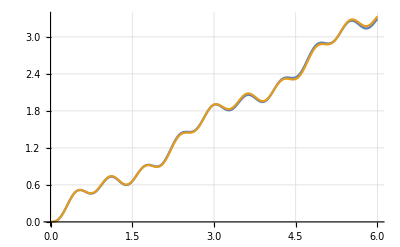

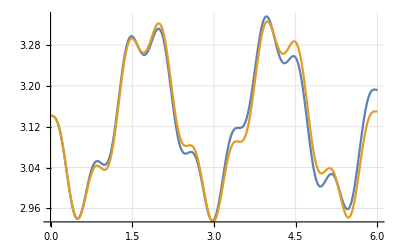

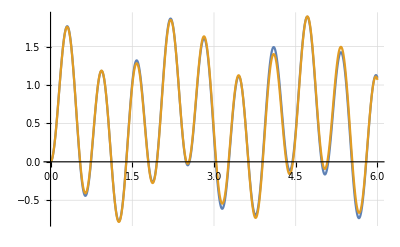

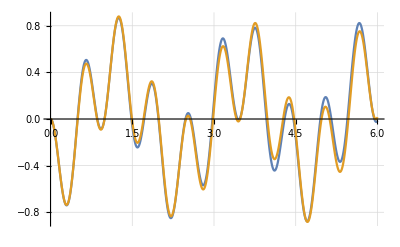

```mathematica
Plot[{SubStar[p][t],Subscript[p, nonlin][t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[θ][t],Subscript[θ, nonlin][t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[ṗ][t],Subscript[ṗ, nonlin][t]},{t,0,6},GridLines->Automatic]
Plot[{SubStar[θ̇][t],Subscript[θ̇, nonlin][t]},{t,0,6},GridLines->Automatic]
```

```mathematica
(*VVEE={ϕ[t],θ[t],ψ[t],p[t],q[t],r[t],X'[t],Y'[t],Z'[t]};
VE=VVEE/.substituicoes2;
eqsdvelocRfixed={eq1final==ϕ'[t],eq2final==θ'[t],eq3final==ψ'[t]};(*//FullSimplify*)
eqsdvelocRbody={eq4final==p'[t],eq5final==q'[t],eq6final==r'[t]};(*//FullSimplify*)
eqsdvelocPfixed={eq7final==X''[t],eq8final==Y''[t],eq9final==Z''[t]};(*//FullSimplify*)
eqsptooper=Flatten[{eqsdvelocRfixed,Drop[eqsdvelocRbody,-1],Drop[eqsdvelocPfixed,-2]}]/.substituicoes2/.substituicoes3;
eqsptooper2=Flatten[{eqsdvelocRfixed,eqsdvelocRbody,eqsdvelocPfixed}]/.substituicoes2;*)
eqsdvelocPbody={eq1final==u'[t],eq2final==v'[t],eq3final==w'[t]};
eqsdvelocRbody={eq4final==p'[t],eq5final==q'[t],eq6final==r'[t]};(*//FullSimplify*)
eqsdvelocPfixed={eq7final==X'[t],eq8final==Y'[t],eq9final==Z'[t]};(*//FullSimplify*)
eqsdvelocRfixed={eq10final==ϕ'[t],eq11final==θ'[t],eq12final==ψ'[t]};(*//FullSimplify*)
eqsptooper=Flatten[{eqsdvelocRfixed,Drop[eqsdvelocRbody,-1],Drop[eqsdvelocPfixed,-2]}]/.substituicoes2/.substituicoes3;
eqsptooper2=Flatten[{eqsdvelocPbody,eqsdvelocRbody,eqsdvelocPfixed,eqsdvelocRfixed}]/.substituicoes2
eqsptooper3={eq1final,eq2final,eq3final,eq4final,eq5final(*,eq6final*),eq7final,eq8final,eq9final,eq10final,eq11final,eq12final}/.substituicoes2;
eqsptooper3/.substituicoes3//MatrixForm
```

```mathematica
vars1={dpdt,dqdt,drdt,dϕdt,dθdt,dψdt,ddXdt,ddYdt,ddZdt};
vars2={ṗ,q̇,ṙ,ϕ̇,θ̇,ψ̇,Ẍ,Ÿ,Z̈};
vars3={ϕ[t],θ[t],ψ[t],p[t],q[t],r[t]};
vars4={ϕ,θ,ψ,u,v,w,p,q,r};
vars5={{ϕ,0},{θ,0},{ψ,0},{u,0},{v,0},{w,0},{p,0},{q,0},{r,0},{X,0},{Y,0},{Z,1}};
eqteste=eqsptooper3/.{ṗ->0,q̇->0,ṙ->0,ϕ̇->0,θ̇->0,ψ̇->0,Ẋ->0,Ẏ->0,Ż->0}/.substituicoes3
zeros={0,0,0,0,0,0,0,0,0,0,0};
```

{r v-q w+9.81 Sin[θ],-r u+p w-9.81 Cos[θ] Sin[ϕ],q u-p v-98.3117 Cos[θ] Sin[ϕ],-2.76049 q-0.753086 q r,2.76049 p+0.753086 p r,u Cos[θ] Cos[ψ]+w Cos[ϕ] Cos[ψ] Sin[θ]+v Cos[ψ] Sin[θ] Sin[ϕ]-v Cos[ϕ] Sin[ψ]+w Sin[ϕ] Sin[ψ],v Cos[ϕ] Cos[ψ]-w Cos[ψ] Sin[ϕ]+u Cos[θ] Sin[ψ]+w Cos[ϕ] Sin[θ] Sin[ψ]+v Sin[θ] Sin[ϕ] Sin[ψ],w Cos[θ] Cos[ϕ]-u Sin[θ]+v Cos[θ] Sin[ϕ],-((-p-p Cot[ϕ]^2-q Csc[ϕ] Tan[θ]-r Cot[ϕ] Csc[ϕ] Tan[θ])/(1+Cot[ϕ]^2)),-(-q Cos[ϕ]+r Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2),-((-q Csc[ϕ] Sec[θ]-r Cot[ϕ] Csc[ϕ] Sec[θ])/(1+Cot[ϕ]^2))}

```mathematica
eqteste
```

Integer[{r v-q w+9.81 Sin[θ],-r u+p w-9.81 Cos[θ] Sin[ϕ],q u-p v-98.3117 Cos[θ] Sin[ϕ],-2.76049 q-0.753086 q r,2.76049 p+0.753086 p r,u Cos[θ] Cos[ψ]+w Cos[ϕ] Cos[ψ] Sin[θ]+v Cos[ψ] Sin[θ] Sin[ϕ]-v Cos[ϕ] Sin[ψ]+w Sin[ϕ] Sin[ψ],v Cos[ϕ] Cos[ψ]-w Cos[ψ] Sin[ϕ]+u Cos[θ] Sin[ψ]+w Cos[ϕ] Sin[θ] Sin[ψ]+v Sin[θ] Sin[ϕ] Sin[ψ],w Cos[θ] Cos[ϕ]-u Sin[θ]+v Cos[θ] Sin[ϕ],-((-p-p Cot[ϕ]^2-q Csc[ϕ] Tan[θ]-r Cot[ϕ] Csc[ϕ] Tan[θ])/(1+Cot[ϕ]^2)),-(-q Cos[ϕ]+r Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2),-((-q Csc[ϕ] Sec[θ]-r Cot[ϕ] Csc[ϕ] Sec[θ])/(1+Cot[ϕ]^2))}]

```mathematica
sols=Reduce[eqteste==zeros,vars4](*//MatrixForm*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

```mathematica
sols//FullSimplify
```

g==0&&p==0&&q==0&&r==0&&u==0&&v==0&&w==0&&((π+2 π C[1]==θ&&((Ixx≠0&&((Iyy≠0&&m Tan[ϕ/2]≠0)||(JJ_TP==0&&Iyy m Tan[ϕ/2]≠0)))||(JJ_TP==0&&(Ixx Iyy m Tan[ϕ/2]≠0||(Iyy≠0&&Ixx m Tan[ϕ/2]≠0))))&&(((C[1]|C[2])∈ℤ&&π+2 π C[2]==ψ&&1/2 (-1+ϕ/π)∉ℤ)||(C[1]∈ℤ&&(1/2 (-1+ϕ/π)|1/2 (-1+ψ/π))∉ℤ)))||(((Ixx≠0&&((Iyy≠0&&m (-1+Tan[θ/2]^2) Tan[ϕ/2]≠0)||(JJ_TP==0&&Iyy m (-1+Tan[θ/2]^2) Tan[ϕ/2]≠0)))||(JJ_TP==0&&(Ixx Iyy m (-1+Tan[θ/2]^2) Tan[ϕ/2]≠0||(Iyy≠0&&Ixx m (-1+Tan[θ/2]^2) Tan[ϕ/2]≠0))))&&((π+2 π C[1]==ψ&&(1/2 (-1+θ/π)|1/2 (-1+ϕ/π))∉ℤ&&C[1]∈ℤ)||(1/2 (-1+θ/π)|1/2 (-1+ϕ/π)|1/2 (-1+ψ/π))∉ℤ)))

```mathematica
eqteste==zeros
```

{r v-q w+9.81 Sin[θ],-r u+p w-9.81 Cos[θ] Sin[ϕ],q u-p v-98.3117 Cos[θ] Sin[ϕ],-2.76049 q-0.753086 q r,2.76049 p+0.753086 p r,u Cos[θ] Cos[ψ]+w Cos[ϕ] Cos[ψ] Sin[θ]+v Cos[ψ] Sin[θ] Sin[ϕ]-v Cos[ϕ] Sin[ψ]+w Sin[ϕ] Sin[ψ],v Cos[ϕ] Cos[ψ]-w Cos[ψ] Sin[ϕ]+u Cos[θ] Sin[ψ]+w Cos[ϕ] Sin[θ] Sin[ψ]+v Sin[θ] Sin[ϕ] Sin[ψ],w Cos[θ] Cos[ϕ]-u Sin[θ]+v Cos[θ] Sin[ϕ],-((-p-p Cot[ϕ]^2-q Csc[ϕ] Tan[θ]-r Cot[ϕ] Csc[ϕ] Tan[θ])/(1+Cot[ϕ]^2)),-(-q Cos[ϕ]+r Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2),-((-q Csc[ϕ] Sec[θ]-r Cot[ϕ] Csc[ϕ] Sec[θ])/(1+Cot[ϕ]^2))}=={0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FindRoot[{r v-q w+g Sin[θ]==u̇,-r u+p w-g Cos[θ] Sin[ϕ]==v̇,q u-p v-(184900 b g Cos[θ] Sin[ϕ])/m==ẇ,((Iyy-Izz) q r)/Ixx-(215 q Subscript[JJ, TP])/Ixx==0,((-Ixx+Izz) p r)/Iyy+(215 p Subscript[JJ, TP])/Iyy==0,((Ixx-Iyy) p q)/Izz==0,u Cos[θ] Cos[ψ]+w Cos[ϕ] Cos[ψ] Sin[θ]+v Cos[ψ] Sin[θ] Sin[ϕ]-v Cos[ϕ] Sin[ψ]+w Sin[ϕ] Sin[ψ]==0,v Cos[ϕ] Cos[ψ]-w Cos[ψ] Sin[ϕ]+u Cos[θ] Sin[ψ]+w Cos[ϕ] Sin[θ] Sin[ψ]+v Sin[θ] Sin[ϕ] Sin[ψ]==0,w Cos[θ] Cos[ϕ]-u Sin[θ]+v Cos[θ] Sin[ϕ]==0,-((-p-p Cot[ϕ]^2-q Csc[ϕ] Tan[θ]-r Cot[ϕ] Csc[ϕ] Tan[θ])/(1+Cot[ϕ]^2))==0,-(-q Cos[ϕ]+r Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2)==0,-((-q Csc[ϕ] Sec[θ]-r Cot[ϕ] Csc[ϕ] Sec[θ])/(1+Cot[ϕ]^2))==0},{{ϕ,0},{θ,0},{ψ,0},{u,0},{v,0},{w,0},{p,0},{q,0},{r,0}}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.-1. OverDot[0.,1.],0.-1. OverDot[0.,1.],0.-1. OverDot[0.,1.],0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {12} at {ϕ,θ,ψ,u,v,w,p,q,r} = {0.,0.,0.,0.,0.,0.,0.,0.,0.}.

(-(-p-p Cot[ϕ]^2-q Csc[ϕ] Tan[θ]-r Cot[ϕ] Csc[ϕ] Tan[θ])/(1+Cot[ϕ]^2)==0
-(-q Cos[ϕ]+r Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2)==0
-(-q Csc[ϕ] Sec[θ]-r Cot[ϕ] Csc[ϕ] Sec[θ])/(1+Cot[ϕ]^2)==0
((Iyy-Izz) q r)/Ixx-(215 q JJ_TP)/Ixx==0
((-Ixx+Izz) p r)/Iyy+(215 p JJ_TP)/Iyy==0
((Ixx-Iyy) p q)/Izz==0
(184900 b (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]))/m==0
(184900 b (-Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ]))/m==0
-g+(184900 b Cos[θ] Cos[ϕ])/m==0)

```mathematica
FindRoot[eqsptooper2/.{ṗ->0,q̇->0,ṙ->0,ϕ̇->0,θ̇->0,ψ̇->0,Ẍ->0,Ÿ->0,Z̈->0,ϕ[t]->ϕ,θ[t]->θ,ψ[t]->ψ,p[t]->p,q[t]->q,r[t]->r},{ϕ,0},{θ,0},{ψ,0},{p,0},{q,0},{r,0}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate,0.,Indeterminate,0.,0.,0.,0.,0.,-1. g+(184900. b)/m} is not a list of numbers with dimensions {9} at {ϕ,θ,ψ,p,q,r} = {0.,0.,0.,0.,0.,0.}.

FindRoot[eqsptooper2/.{ṗ→0,q̇→0,ṙ→0,ϕ̇→0,θ̇→0,ψ̇→0,Ẍ→0,Ÿ→0,Z̈→0,ϕ[t]→ϕ,θ[t]→θ,ψ[t]→ψ,p[t]→p,q[t]→q,r[t]→r},{ϕ,0},{θ,0},{ψ,0},{p,0},{q,0},{r,0}]

```mathematica
e22={x'[t]==-y[t]-z[t],x[0]==-0.04,y'[t]==x[t]+.425 y[t],y[0]==-0.30,z'[t]==2-z[t] (4-x[t]),z[0]==0.52};
```

```mathematica
e22//MatrixForm
e23={x[t],y[t],z[t]}/.Flatten[NDSolve[e22,{x,y,z},{t,0,25}]];
e24={x[t],y[t],z[t]}/.Flatten[NDSolve[e22,{x,y,z},{t,0,25},Method->ExplicitRungeKutta]];
ParametricPlot3D[Evaluate[{e23,e24}],{t,0,25},PlotPoints->1000,PlotRange->All]
```

(x'[t]==-y[t]-z[t]
x[0]==-0.04
y'[t]==x[t]+0.425 y[t]
y[0]==-0.3
z'[t]==2-(4-x[t]) z[t]
z[0]==0.52)

-Graphics3D-

Here is a matrix:

```mathematica
u={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
u={{a1,b1,c1},{d1,e1,f1},{g1,h1,i1}};
v={{a2,b2,c2},{d2,e2,f2},{g2,h2,i2}};
w={{a3,b3,c3},{d3,e3,f3},{g3,h3,i3}};
```

Flatten an array of blocks with the shape of u into a single matrix:

```mathematica
Flatten[{{u,0 u},{0 u,v}},{{1,3},{2,4}}]//MatrixForm
```

(a1 | b1 | c1 | 0 | 0 | 0
d1 | e1 | f1 | 0 | 0 | 0
g1 | h1 | i1 | 0 | 0 | 0
0 | 0 | 0 | a2 | b2 | c2
0 | 0 | 0 | d2 | e2 | f2
0 | 0 | 0 | g2 | h2 | i2)

Flatten into a single matrix, effectively using the transpose of the blocks:

```mathematica
Flatten[{{u,0 u},{0 u,u}},{{1,4},{2,3}}]//MatrixForm
```

(a | d | g | 0 | 0 | 0
b | e | h | 0 | 0 | 0
c | f | i | 0 | 0 | 0
0 | 0 | 0 | a | d | g
0 | 0 | 0 | b | e | h
0 | 0 | 0 | c | f | i)

```mathematica
p[t]=.;θ[t]=.;p'[t]=.;θ'[t]=.;u[t]=.;
```

StateSpaceModel |

| StateSpaceModelpaclet:ref/StateSpaceModel[{a,b,c,d}] 
represents the standard state-space model with state matrix a, input matrix b, output matrix c, and transmission matrix d.
 | StateSpaceModelpaclet:ref/StateSpaceModel[{a,b,c,d,e}]
represents a descriptor state-space model with descriptor matrix e.
 | StateSpaceModelpaclet:ref/StateSpaceModel[sys] 
gives a state-space model corresponding to the systems model sys.
 | StateSpaceModelpaclet:ref/StateSpaceModel[eqns,{{x_1,x_10},…},{{u_1,u_10},…},{g_1,…},τ]
gives the state-space model obtained by Taylor linearization about the point (x_i_0,u_i_0) of the differential or difference equations eqns with outputs g_i and independent variable τ.

StateSpaceModelpaclet:ref/StateSpaceModel can represent scalar and multivariate systems in continuous or discrete time.

Time delays can be represented in any state-space model, by using SystemsModelDelaypaclet:ref/SystemsModelDelay in any of the matrices.

A continuous-time system modeled by the equations x'(t)==a.x(t)+b.u(t), y(t)==c.x(t)+d.u(t) with states x∈ℝ^n, control inputs u∈ℝ^p, and outputs y∈ℝ^q can be specified as StateSpaceModelpaclet:ref/StateSpaceModel[{a,b,c,d}].

A discrete-time system modeled by the equations x(k+1)==a.x(k)+b.u(k), y(k)==c.x(k)+d.u(k) with states x∈ℝ^n, control inputs u∈ℝ^p, outputs y∈ℝ^q, and sampling period τ can be specified as StateSpaceModelpaclet:ref/StateSpaceModel[{a,b,c,d},SamplingPeriodpaclet:ref/SamplingPeriod->τ].

Continuous-time and discrete-time descriptor state-space systems can be specified as follows:

| StateSpaceModel[{a,b,c,d,e}] | e.x'(t)==a.x(t)+b.u(t), y(t)==c.x(t)+d.u(t)
       | StateSpaceModel[{a,b,c,d,e},SamplingPeriodpaclet:ref/SamplingPeriod->τ] | e.x(k+1)==a.x(k)+b.u(k), y(k)==c.x(k)+d.u(k)

For a system with n states, p inputs, and q outputs, the matrices a, b, c, d and e should have dimensions {n,n}, {n,p}, {q,n}, {q,p}, and {n,n}.

The following short inputs can be used:

| StateSpaceModel[{a,b,c}] | x'(t)==a.x(t)+b.u(t), y(t)==c.x(t)
       | StateSpaceModel[{a,b}] | x'(t)==a.x(t)+b.u(t), y(t)==x(t)
       | StateSpaceModel[{a,b,c,Automaticpaclet:ref/Automatic,e}] | e.x'(t)==a.x(t)+b.u(t), y(t)==c.x(t)
       | StateSpaceModel[{a,b,Automaticpaclet:ref/Automatic,Automaticpaclet:ref/Automatic,e}] | e.x'(t)==a.x(t)+b.u(t), y(t)==x(t)

In StateSpaceModelpaclet:ref/StateSpaceModel[sys] the following systems can be converted:

| AffineStateSpaceModelpaclet:ref/AffineStateSpaceModel | approximate Taylor conversion
       | NonlinearStateSpaceModelpaclet:ref/NonlinearStateSpaceModel | approximate Taylor conversion
       | TransferFunctionModelpaclet:ref/TransferFunctionModel | exact conversion

When converting from transfer-function model sys, the controllable realization is used.

For equational input, default linearization points x_i_0 and u_j_0 are taken to be zero.

The following options can be given:

| SamplingPeriodpaclet:ref/SamplingPeriod | Automaticpaclet:ref/Automatic | the sampling period
       | StateSpaceRealizationpaclet:ref/StateSpaceRealization | Automaticpaclet:ref/Automatic | the canonical realization
       | DescriptorStateSpacepaclet:ref/DescriptorStateSpace | Automaticpaclet:ref/Automatic | standard or descriptor realization
       | SystemsModelLabelspaclet:ref/SystemsModelLabels | Automaticpaclet:ref/Automatic | the labels for the input, output, and state variables

## Examples (67)

### Basic Examples (5)

A state-space model of an integrator:

```mathematica
StateSpaceModel[{{{0}},{{1}},{{1}}}]
```

0110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

A second-order single-input, single-output system:

```mathematica
StateSpaceModel[{{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}},{{Subscript[b, 1]},{Subscript[b, 2]}},{{Subscript[c, 1],Subscript[c, 2]}}}]
```

a_1a_2b_1a_3a_4b_2c_1c_20StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

The state-space model of a transfer-function object:

```mathematica
StateSpaceModel[1/(-a+s)1/(-b+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s2111$CellContext`a$CellContext`b1FalseFalseFalseAutomaticNoneAutomatic]
```

a0100b011100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNoneAutomatic

The state-space model of a system with sampling period τ:

```mathematica
StateSpaceModel[{DiagonalMatrix[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}],Table[1,{3},{1}], Table[1,{1},{3}]},SamplingPeriod->τ]
```

a_10010a_20100a_311110τStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

The state-space model of a set of ODEs:

```mathematica
StateSpaceModel[{m Subscript[ϕ, 1]''[t]-m Ω^2 Subscript[ϕ, 1][t]+(Subscript[ϕ, 1][t]-Subscript[ϕ, 2][t])k/2==0,m Subscript[ϕ, 2]''[t]-m Ω^2 Subscript[ϕ, 2][t]-(Subscript[ϕ, 1][t]-Subscript[ϕ, 2][t])k/2==u[t]},{{Subscript[ϕ, 1]'[t],0},{Subscript[ϕ, 1][t],0},{Subscript[ϕ, 2][t],0},{Subscript[ϕ, 2]'[t],0}},{{u[t],0}},{Subscript[ϕ, 2][t]},t]
```

0-(k-2 m Ω^2)/(2 m)k/(2 m)0010000000100k/(2 m)-(k-2 m Ω^2)/(2 m)01/m00100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNone,{{ϕ_1[t],0},x_1,{ϕ_2[t],0},x_2},{{u[t],0}},Automatic,t

### Scope (31)

#### Basic Uses (17)

A second-order system:

```mathematica
StateSpaceModel[{{{-1,0},{0,-2}},{{1},{2}},{{1,1}},{{1}}}]
```

-1010-22111StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

A fourth-order system:

```mathematica
StateSpaceModel[{{{-1,0,1,3},{0,-2,1,2},{-1,0,1,0},{0,0,1,-1}}, {{1},{-1},{0},{0}},{{1,0,0,1}},{{0}}}]
```

-101310-212-1-10100001-1010010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

A system with two inputs:

```mathematica
StateSpaceModel[{{{1,-1,0},{-1,4,1},{-2,2,1}}, {{-1, 0.2},{-1, 1},{0, 2}}, {{1, -1, 0}}}]
```

1-10-10.2-141-11-221021-1000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2131FalseFalseFalseAutomaticNoneAutomatic

A system with two outputs:

```mathematica
StateSpaceModel[{{{-1,2,2,0},{-1,-2,-1,-1},{-2,0,2,-2},{2,1,0,-1}}, {{1},{2},{0},{-1}},{{1,-1,0,0},{0,0,1,-1}},{{0},{0}}}]
```

-12201-1-2-1-12-202-20210-1-11-1000001-10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNoneAutomatic

Direct feedthrough is assumed to be zero:

```mathematica
StateSpaceModel[{{{-1,2},{1,-4}},{{1},{1}},{{1,1}}}]
```

-1211-41110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

Specify feedthrough:

```mathematica
StateSpaceModel[{{{-1,1},{2,-1}},{{1},{1}},{{1,1}},{{f}}}]
```

-1112-1111fStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

The feedthrough is the sum of the inputs:

```mathematica
StateSpaceModel[{{{1,0},{-2,-1}},{{-2,1,-1},{1,-1,-1}},{{-1,0}},{{1,1,1}}}]
```

10-21-1-2-11-1-1-10111StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic3121FalseFalseFalseAutomaticNoneAutomatic

A discrete-time model:

```mathematica
StateSpaceModel[{{{0,1,0,0},{-0.1,-0.001,0.1,0.001},{0,0,0,1}, {0.05,0.005,-0.5,-0.005}},{{0},{0},{0},{1}},{{1,0,0,0 }}}, SamplingPeriod->0.1]
```

01000-0.1-0.0010.10.0010000100.050.005-0.5-0.0051100000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

A symbolic model:

```mathematica
StateSpaceModel[{{{0,1},{-k/m,-c/m}},{{c/m},{k/m-(c/m)^2}},{{1,0}}}]
```

01c/m-k/m-c/m-c^2/m^2+k/m100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

The state-space model of a transfer function:

```mathematica
StateSpaceModel[TransferFunctionModel[{{1/s,1/((s+1)(s+3))}},s]]
```

00010001000-3-40111000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2131FalseFalseFalseAutomaticNoneAutomatic

Perform symbolic conversions:

```mathematica
StateSpaceModel[TransferFunctionModel[ 1/(a s^2+b s+c),s]]
```

010-c/a-b/a11/a00StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

Taylor linearize an AffineStateSpaceModelpaclet:ref/AffineStateSpaceModel:

```mathematica
StateSpaceModel[Subscript[x, 1]+Subscript[x, 2]^2-Subscript[x, 1] Subscript[x, 2]1Subscript[x, 1]Subscript[x, 1]0Subscript[x, 1]Subscript[x, 2] 211111NoneFalseFalseFalseFalse{u}Automatic]
```

101000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x_1,0},{x_2,0}},{{u,0}},{Automatic}

The linearization of an AffineStateSpaceModelpaclet:ref/AffineStateSpaceModel with nonzero equilibrium values:

```mathematica
StateSpaceModel[Subscript[x, 1]+2 Subscript[x, 2]+Subscript[x, 2]^21-Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 1] Subscript[x, 2]1Subscript[x, 1]-1+Subscript[x, 1]0{Subscript[x, 1],1}{Subscript[x, 2],-1} 211111NoneFalseFalseFalseFalse{u}Automatic]
```

101001100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x_1,0},{x_2,0}},{{u,0}},{Automatic}

Taylor linearize a NonlinearStateSpaceModelpaclet:ref/NonlinearStateSpaceModel:

```mathematica
StateSpaceModel[-1+u x-1+x{x,1} 1111NoneFalseFalseFalse{{u,1}}Automatic]
```

1110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneNone,{{x,0}},{{u,0}},{Automatic}

Linearize a nonlinear state-space model:

```mathematica
StateSpaceModel[{{x2-x3^2,x3+2 x1^2 x3+2 x3 u,x1^2+u,-x1-x1^2 x2},{x1+u}},{{x1,0},{x2,0},{x3,0},{x4,0}},{{u,0}}]
```

010000010000001-1000010001StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNone,{{x1,0},{x2,0},{x3,0},{x4,0}},{{u,0}}

The linear state-space model of an ODE:

```mathematica
StateSpaceModel[{Subscript[a, 3] x'''[t]+Subscript[a, 2] x''[t]+Subscript[a, 1] x'[t]+Subscript[a, 0] x[t]==f[t]},{{x[t],0},{x'[t],0},{x''[t],0}},{{f[t],0}},{x[t]},t]
```

01000010-a_0/a_3-a_1/a_3-a_2/a_31/a_31000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNone,{{x[t],0},x_1,x_2},{{f[t],0}},Automatic,t

An ODE with a derivative control term:

```mathematica
StateSpaceModel[{Subscript[K, 3] ϕ'''[t]+Subscript[K, 2] ϕ''[t]+Subscript[K, 1] ϕ'[t]+Subscript[K, 0] ϕ[t]==Subscript[K, a] δ'[t]+Subscript[K, b] δ[t]},{{ϕ[t],0},{ϕ'[t],0},{ϕ''[t],0}},{{δ[t],0}},{ϕ[t]},t]
```

0100001K_a/K_3-K_0/K_3-K_1/K_3-K_2/K_3-((K_2 K_a)/K_3-K_b)/K_31000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNone,{{ϕ[t],0},x_1,x_2},{{δ[t],0}},Automatic,t

Use Normalpaclet:ref/Normal to obtain the matrices:

```mathematica
{aa,bb,cc,dd}=Normal[StateSpaceModel[{Array[a,{2,2}],Array[b,{2,1}],Array[c,{1,2}],Array[d,{1,1}]}]]
```

{{{a[1,1],a[1,2]},{a[2,1],a[2,2]}},{{b[1,1]},{b[2,1]}},{{c[1,1],c[1,2]}},{{d[1,1]}}}

#### Descriptor Systems (8)

A descriptor system:

```mathematica
StateSpaceModel[{{{a}},{{b}},{{c}},{{d}},{{e}}}]
```

eabcdStateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseTrueAutomaticNoneAutomatic

A singular descriptor system:

```mathematica
StateSpaceModel[{{{-3,1},{0,1}},{{0},{1}},{{1,0}},{{0}},{{1,1},{0,0}}}]
```

11-31000011100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNoneAutomatic

Use Automaticpaclet:ref/Automatic to create a descriptor system with default outputs:

```mathematica
StateSpaceModel[{{{1,0},{-2,-1}},{{1},{0}},Automatic,Automatic,{{1,-.5},{0,1}}}]
```

1-0.510101-2-10100010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1221FalseFalseTrueAutomaticNoneAutomatic

Systems can include both differential and algebraic equations:

```mathematica
dynamics=Subscript[x, 1]'[t]==-3 Subscript[x, 1][t]+Subscript[x, 2][t]+u[t];
constraint=Subscript[x, 2][t]+Subscript[x, 1][t]==0;
```

The resulting model has a singular descriptor matrix:

```mathematica
StateSpaceModel[{dynamics,constraint},{Subscript[x, 1][t],Subscript[x, 2][t]},{u[t]},Subscript[x, 1][t],t]
```

-103-1-100110100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNone,{{x_2[t],0},{x_1[t],0}},{{u[t],0}},Automatic,t

A discrete-time descriptor system from difference equations:

```mathematica
StateSpaceModel[{x[k+1]==.5x[k],y[k]==-x[k]+u[k]},{x[k],y[k]},{u[k]},{x[k]},k]
```

-10-0.50.0001.1.-11001StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNone,{{y[k],0},{x[k],0}},{{u[k],0}},Automatic,k

A zero descriptor matrix gives an algebraic system:

```mathematica
StateSpaceModel[{{{-3}},{{1}},{{2}},{{1/2}},{{0}}}]
```

0-3121/2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseTrueAutomaticNoneAutomatic

For descriptor systems, Normalpaclet:ref/Normal returns all five matrices:

```mathematica
MatrixForm/@Normal[Subscript[e, 1]Subscript[e, 2]Subscript[a, 1]Subscript[a, 2]Subscript[b, 1]Subscript[e, 3]Subscript[e, 4]Subscript[a, 3]Subscript[a, 4]Subscript[b, 2]Subscript[c, 1]Subscript[c, 2]Subscript[d, 1]]
```

{(a_1 | a_2
a_3 | a_4),(b_1
b_2),(c_1 | c_2),(d_1),(e_1 | e_2
e_3 | e_4)}

Invert the descriptor matrix to create a standard state-space model:

```mathematica
StateSpaceModel[Subscript[e, 1]0Subscript[a, 1]0Subscript[b, 1]0Subscript[e, 2]0Subscript[a, 2]Subscript[b, 2]Subscript[c, 1]Subscript[c, 2]d, DescriptorStateSpace->False]
```

a_1/e_10b_1/e_10a_2/e_2b_2/e_2c_1c_2dStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

#### Time-Delay Systems (5)

An output-delay system:

```mathematica
StateSpaceModel[{{{a}},{{b}},{{c SystemsModelDelay[3]}},{{d}},{{e}}}]
```

eabc 3dStateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseTrueAutomaticNoneAutomatic

A system with two input delays:

```mathematica
StateSpaceModel[{{{0, 1}, {-1, -(1/2)}}, {{SystemsModelDelay[1]/2}, {2*SystemsModelDelay[2]}}, {{1, 0}}, 
   {{0}}}, SamplingPeriod -> None, SystemsModelLabels -> None]
```

011/2-1-1/22 2100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

A discrete-time system with a delay in the state matrix:

```mathematica
StateSpaceModel[{{{Subscript[a\[SystemsModelDelay], δ]}},{{b}},{{c}}},SamplingPeriod->T]
```

(a\[SystemsModelDelay])_δbc0TStateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

Create a time delay system directly from delay-differential equations:

```mathematica
StateSpaceModel[{x'[t]==-x[t-3]+u[t]},{x[t]},{u[t]},{x[t]},t]
```

-3110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{{x[t],0}},{{u[t],0}},Automatic,t

Delays in the differential terms create neutral time-delay systems:

```mathematica
eqs={Subscript[x, 1]'[t]==-.5 Subscript[x, 1][t]+Subscript[x, 2][t],Subscript[x, 2]'[t]==-.2 Subscript[x, 1]'[t-2]-3 Subscript[x, 2][t]+u[t]};
```

```mathematica
StateSpaceModel[eqs,{Subscript[x, 1][t],Subscript[x, 2][t]},{u[t]},Subscript[x, 1][t],t]
```

1.0.-0.51.0.0.+0.2 21.0.-3.1.100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNone,{x_1,{x_1[t],0}},{{u[t],0}},Automatic,t

### Generalizations & Extensions (2)

If the transmission matrix is not specified, the model is assumed to have zero feedthrough:

```mathematica
Normal[StateSpaceModel[{{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}},{{Subscript[b, 1]},{Subscript[b, 2]}},{{Subscript[c, 1],Subscript[c, 2]}}}]]//Last
```

{{0}}

If the outputs are not specified, they are assumed to be the states:

```mathematica
Normal[StateSpaceModel[{{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}},{{Subscript[b, 1]},{Subscript[b, 2]}}}]][[3;;4]]
```

{{{1,0},{0,1}},{{0},{0}}}

### Options (8)

#### SamplingPeriod (4)

A continuous-time model:

```mathematica
StateSpaceModel[{{{0,1},{-0.01,-1}},{{1},{-1}},{{1,0}}}]
```

011-0.01-1-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

A discrete-time model with sampling period 2:

```mathematica
StateSpaceModel[{{{1,-1},{-0.1,-1}},{{0},{1}},{{1,1}}},SamplingPeriod->2]
```

1-10-0.1-111102StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

SamplingPeriodpaclet:ref/SamplingPeriod is Nonepaclet:ref/None for continuous-time systems:

```mathematica
StateSpaceModel[{{{0,1},{-0.01,-1}},{{1}, {-1}},{{1, 0}}},SamplingPeriod->None]
```

011-0.01-1-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

A symbolic sampling period:

```mathematica
ss=StateSpaceModel[{{{1,0.5},{-0.5,0.5}},{{1},{0}},{{1,0}}},SamplingPeriod->T]
```

10.51-0.50.50100TStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

Specify a numerical value:

```mathematica
ss/.T->0.2
```

10.51-0.50.501000.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

#### StateSpaceRealization (3)

The controllable companion form:

```mathematica
tf=1/(4+3 s+2 s^2+s^3)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11141FalseFalseFalseAutomaticNoneAutomatic;
```

```mathematica
ssc=StateSpaceModel[tf]
```

01000010-4-3-211000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

The observable companion form:

```mathematica
sso=StateSpaceModel[tf,StateSpaceRealization->"ObservableCompanion"]
```

00-4110-3001-200010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

The Jordan form:

```mathematica
Last[JordanModelDecomposition[ssc]]//N//Chop
```

-0.174685-1.54687 ⅈ000.201985-0.305653 ⅈ0-1.6506300.59602900-0.174685+1.54687 ⅈ0.201985+0.305653 ⅈ-0.402265-0.0920278 ⅈ0.367029-0.402265+0.0920278 ⅈ0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

The realizations of a discrete-time model:

```mathematica
tf=(b3+b2 z+b1 z^2+b0 z^3)/(a3+a2 z+a1 z^2+z^3)TTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11$CellContext`b3$CellContext`a31FalseFalseFalseAutomaticNoneAutomatic;
```

```mathematica
ssc=StateSpaceModel[tf]
```

01000010-a3-a2-a11-a3 b0+b3-a2 b0+b2-a1 b0+b1b0TStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
sso=StateSpaceModel[tf,StateSpaceRealization->"ObservableCompanion"]
```

00-a3-a3 b0+b310-a2-a2 b0+b201-a1-a1 b0+b1001b0TStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Last[JordanModelDecomposition[sso/.{b0->1,b1->2,b2->3,b3->4,a1->-1,a2->-2,a3->-3}]]//N//Chop
```

-0.687212+0.889497 ⅈ00-0.260277+0.403046 ⅈ0-0.687212-0.889497 ⅈ0-0.260277-0.403046 ⅈ002.374423.520551.1.1.1.TStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

#### SystemsModelLabels (1)

Label the inputs, outputs, and states:

```mathematica
StateSpaceModel[{{{0,0,1},{0,-1.4,1},{0,-10,-0.1}},{{0,0},{-0.707,-0.2},{3,-1}},{{1,0,0},{0,0,1},{1,-1,0}}},SystemsModelLabels->{{"δ_c","δ_f"},{"θ","θ^•","γ"},{"θ","α","θ^•"}}]
```

001000-1.41-0.707-0.20-10-0.13-110000001001-1000δ_cδ_fθθ^•γθαθ^•StateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3δ_cδ_fθθ^•γθαθ^•IdentityAutomatic23311112212223313233TrueTrueFalseAutomaticδ_cδ_fθθ^•γθαθ^•Automatic

### Applications (7)

#### Chemical Systems (1)

Equations governing the concentration in a two-stage chemical reactor with constant flow rate:

```mathematica
stage1=Subscript[v, 1] Subscript[c, 1]'[t] == Subscript[q, 1] Subscript[c, f1][t]+r Subscript[c, 2][t-α]+Subscript[q, d] Subscript[c, d][t] - (Subscript[q, 1]+r+Subscript[q, d])Subscript[c, 1][t]-Subscript[v, 1] Subscript[k, 1] Subscript[c, 1][t];
stage2=Subscript[v, 2] Subscript[c, 2]'[t]== (Subscript[q, 1]+r+Subscript[q, d]-Subscript[q, p1])Subscript[c, 1][t] +Subscript[q, 2] Subscript[c, f2][t]-(Subscript[q, p2]+r)Subscript[c, 2][t] - Subscript[v, 2] Subscript[k, 2] Subscript[c, 2][t];
```

A state-space model for the reactor:

```mathematica
reactor=StateSpaceModel[{stage1, stage2},{Subscript[c, 1][t],Subscript[c, 2][t]},{Subscript[c, f1][t],Subscript[c, f2][t],Subscript[c, d][t]},{Subscript[c, 1][t-Subscript[τ, 1]],Subscript[c, 2][t-Subscript[τ, 2]]},t]
```

-(r+q_1+q_d+k_1 v_1)/v_1(r α)/v_1q_1/v_10q_d/v_1-(-r-q_1-q_d+q_p1)/v_2-(r+q_p2+k_2 v_2)/v_20q_2/v_20τ_100000τ_2000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic3221FalseFalseFalseAutomaticNone,{{c_1[t],0},{c_2[t],0}},{{c_f1[t],0},{c_f2[t],0},{c_d[t],0}},Automatic,t

Control the inputs with unity feedback:

```mathematica
closedloop=SystemsModelFeedbackConnect[reactor,{{1,1},{2,2}}]
```

-(r+q_1+q_d+k_1 v_1)/v_1-(q_1 τ_1)/v_1(r α)/v_1q_1/v_10q_d/v_1-(-r-q_1-q_d+q_p1)/v_2-(r+q_p2+k_2 v_2)/v_2-(q_2 τ_2)/v_20q_2/v_20τ_100000τ_2000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic3221FalseFalseFalseAutomaticNone,{{c_1[t],0},{c_2[t],0}},{{u_1,0},{u_2,0},{c_d[t],0}},Automatic,t

Substitute numeric values and simulate the response to a disturbance:

```mathematica
closedloop=closedloop/.{α->1, Subscript[τ, 1]->3, Subscript[τ, 2]->2, Subscript[v, 1]->1, Subscript[v, 2]->1,Subscript[q, 1]->.4, Subscript[q, d]->.6, Subscript[q, 2]->.5, r->.5, Subscript[k, 1]->.5, Subscript[k, 2]->.5, Subscript[q, p1]->1,Subscript[q, p2]->1};
response=OutputResponse[{closedloop,{1,0}},{0,0,0},{t,0,12}];
```

```mathematica
Plot[response,{t,0,12}, PlotRange->All]
```

-Graphics-

#### Electrical Systems (2)

A series resistance-inductance-capacitance (RLC) circuit:

```mathematica
eqns={L q''[t]+R q'[t]+1/C q[t]==V[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{V[t],0}},{q'[t]},t]
```

010-1/(C L)-R/L1/L010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{V[t],0}},Automatic,t

The same RLC circuit modeled as a descriptor state space:

```mathematica
eqns={L i'[t]==Subscript[v, l][t],Subscript[v, c]'[t]==1/C i[t],R i[t]==Subscript[v, r][t],
Subscript[v, l][t]+Subscript[v, c][t]+Subscript[v, r][t]==Subscript[v, s][t]};
```

```mathematica
m2=StateSpaceModel[eqns,{i[t],Subscript[v, l][t],Subscript[v, c][t],Subscript[v, r][t]},{Subscript[v, s][t]},{i[t]},t]
```

-L0000-100000-10-1/C00000000R00-1000000111-110000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseTrueAutomaticNone,{{v_c[t],0},{v_l[t],0},{v_r[t],0},{i[t],0}},{{v_s[t],0}},Automatic,t

Both models are equivalent:

```mathematica
TransferFunctionModel[m1][s]
```

{{s/(L (1/(C L)+(R s)/L+s^2))}}

```mathematica
TransferFunctionModel[m2][s]
```

{{(C (-(-1-C R s-C L s^2)/C+(-1-C s-C R s-C L s^2)/C))/(-1-C R s-C L s^2)}}

```mathematica
Simplify[%%-%]
```

{{0}}

A circuit with two loops modeled with Kirchhoff's laws:

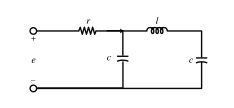

```mathematica
components={L Subscript[i, 2]'[t]==Subscript[v, l][t],Subscript[v, c1]'[t]==(Subscript[i, 1][t])/Subscript[C, 1],Subscript[v, c2]'[t]==(Subscript[i, 2][t])/Subscript[C, 2]};kirchhoff={R (Subscript[i, 1][t]+Subscript[i, 2][t])==Subscript[v, r][t],Subscript[v, c1][t]+Subscript[v, r][t]==Subscript[v, s][t],Subscript[v, c1][t]==Subscript[v, l][t]+Subscript[v, c2][t]};
```

The resulting state-space model includes the algebraic constraints:

```mathematica
StateSpaceModel[Join[components,kirchhoff],{ Subscript[v, c1][t], Subscript[v, c2][t], Subscript[i, 2][t],Subscript[i, 1][t],Subscript[v, r][t], Subscript[v, l][t]}, Subscript[v, s][t], Subscript[v, c2][t],t]
```

00-L00000000-10-100000000-1/C_10000-1000000-1/C_2000000000000RR-100000000100010-10000001-1000-100100000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1161FalseFalseTrueAutomaticNone,{{i_2[t],0},{v_c1[t],0},{v_l[t],0},{i_1[t],0},{v_r[t],0},{v_c2[t],0}},{{v_s[t],0}},Automatic,t

#### Mechanical Systems (4)

Linearize an inverted pendulum model:

```mathematica
StateSpaceModel[{(M+m)x''[t]-m l Sin[θ[t]] θ'[t]^2+m l Cos[θ[t]] θ''[t]==F[t], m x''[t] Cos[θ[t]]+m l θ''[t]==m g Sin[θ[t]]},{{θ[t],0},{θ'[t],0},{x[t],0},{x'[t],0}},{{F[t],0}},{θ[t],x[t]},t]
```

01000-(g (-m-M))/(l M)000-1/(l M)00010-(g m)/M0001/M1000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{θ[t],0},x_1,{x[t],0},x_2},{{F[t],0}},Automatic,t

State-space model of a typical mechanical mass-spring-damper system:

```mathematica
StateSpaceModel[{M x''[t]+C x'[t]+K x[t]==F[t]},{{x[t],0},{x'[t],0}},{{F[t],0}},{x[t]},t]
```

010-K/M-C/M1/M100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x[t],0},x_1},{{F[t],0}},Automatic,t

A two-stage mass-spring-damper system with delayed feedback:

```mathematica
eqns={m2 x2''[t]+b2 (x2'[t]- x1'[t])+k2(x2[t]-x1[t])-g x1[t-τ]==0,m1 x1''[t]+(b1+b2)x1'[t]-b2 x2'[t]+(k1+k2)x1[t] - k2 x2[t]+g x1[t-τ]==0};
```

```mathematica
StateSpaceModel[eqns,{x2[t],x2'[t],x1[t],x1'[t]},{u[t]},{x2[t],x1[t]},t]
```

01000-k2/m2-b2/m2-(-k2-g τ)/m2b2/m2000010k2/m1b2/m1-(k1+k2+g τ)/m1-(b1+b2)/m101000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x2[t],0},x_1,{x1[t],0},x_2},{{u[t],0}},Automatic,t

The cutting force required in a lathe depends on the cutting depth from the previous rotation:

```mathematica
StateSpaceModel[k x[t]+c x'[t]+m x''[t]==-α (f[t]+x[t]-x[t-τ]),{x[t],x'[t]},{f[t]},x[t],t]
```

010-(k+α-α τ)/m-c/m-α/m100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x[t],0},x_1},{{f[t],0}},Automatic,t

### Properties & Relations (14)

The state-space representation of a system is not unique:

```mathematica
{ssm= StateSpaceModel[{{{-2.7121,3.9238},{-4.2371,1.9429}},{{-2.3857},{4.4438}},{{1,1}}}],
ssmt=StateSpaceTransform[ssm,{{-0.842,2.6891},{-4.6641,3.3886}}]}
```

{-2.71213.9238-2.3857-4.23711.94294.4438110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,-4.076983.43454-2.0677-7.232993.30778-1.5346-5.50616.07770StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

Similar state-space models have identical transfer functions:

```mathematica
TransferFunctionModel/@ {ssm,ssmt}
```

{(44.2322+2.0581 s)/(11.3562+0.7692 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1144.2322384200000111.356193891FalseFalseFalseAutomaticNoneAutomatic,(44.2322+2.0581 s)/(11.3562+0.7692 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1144.2322384199999711.3561938900000021FalseFalseFalseAutomaticNoneAutomatic}

The controllable and observable companion forms are duals of each other:

```mathematica
tfm=(s^3 Subscript[b, 0]+s^2 Subscript[b, 1]+s Subscript[b, 2]+Subscript[b, 3])/(s^3+s^2 Subscript[a, 1]+s Subscript[a, 2]+Subscript[a, 3])TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic;
```

```mathematica
{ssc,sso}=Table[StateSpaceModel[tfm,StateSpaceRealization->form],{form,{"ControllableCompanion","ObservableCompanion"}}]
```

{01000010-a_3-a_2-a_11-a_3 b_0+b_3-a_2 b_0+b_2-a_1 b_0+b_1b_0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,00-a_3-a_3 b_0+b_310-a_2-a_2 b_0+b_201-a_1-a_1 b_0+b_1001b_0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}

Compute their dual representations:

```mathematica
Table[Refine[DualSystemsModel[model],{Subscript[b, _],Subscript[a, _]}∈Reals],{model,{ssc,sso}}]
```

{00-a_3-a_3 b_0+b_310-a_2-a_2 b_0+b_201-a_1-a_1 b_0+b_1001b_0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01000010-a_3-a_2-a_11-a_3 b_0+b_3-a_2 b_0+b_2-a_1 b_0+b_1b_0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}

The eigenvalues of the state matrix are invariant:

```mathematica
{ssm= StateSpaceModel[{{{3.5483,-4.1308},{3.1786,2.8758}},{{4.5882},{2.8867}},{{-1.192,-2.7873}}}],
ssmt=StateSpaceTransform[ssm,{{2.3878,-3.243},{-3.9273,-3.4311}}]}
```

{3.5483-4.13084.58823.17862.87582.8867-1.192-2.78730StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,4.622573.563290.304888-4.211461.80153-1.190318.1003113.42920StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
Map[Composition[Eigenvalues,First,Normal],{ssm,ssmt}]
```

{{3.21205+3.60792 ⅈ,3.21205-3.60792 ⅈ},{3.21205+3.60792 ⅈ,3.21205-3.60792 ⅈ}}

The state matrix satisfies its characteristic equation (Cayley–Hamilton theorem):

```mathematica
ssm=StateSpaceModel[{Array[a,{3,3}],Array[b,{3,1}],Array[c,{1,3}],{{d[1,1]}}}]
```

a[1,1]a[1,2]a[1,3]b[1,1]a[2,1]a[2,2]a[2,3]b[2,1]a[3,1]a[3,2]a[3,3]b[3,1]c[1,1]c[1,2]c[1,3]d[1,1]StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(A=Composition[First,Normal][ssm])//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3]
a[2,1] | a[2,2] | a[2,3]
a[3,1] | a[3,2] | a[3,3])

```mathematica
CoefficientList[CharacteristicPolynomial[A,s],s].Table[MatrixPower[A,n],{n,0,3}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

A controllable system:

```mathematica
StateSpaceModel[{DiagonalMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}],{{Subscript[b, 1]},{Subscript[b, 2]},{Subscript[b, 3]}}}]
ControllableModelQ[%]
```

λ_100b_10λ_20b_200λ_3b_3StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-331FalseFalseFalseAutomaticNoneAutomatic

True

An uncontrollable system:

```mathematica
StateSpaceModel[{DiagonalMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}],{{Subscript[b, 1]},{Subscript[b, 2]},{0}}}]
ControllableModelQ[%]
```

λ_100b_10λ_20b_200λ_30StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-331FalseFalseFalseAutomaticNoneAutomatic

False

A controllable system with non-distinct eigenvalues:

```mathematica
StateSpaceModel[{{{Subscript[λ, 1],1,0},{0,Subscript[λ, 1],0},{0,0,Subscript[λ, 3]}},{{0},{Subscript[b, 2]},{Subscript[b, 3]}}}]
ControllableModelQ[%]
```

λ_11000λ_10b_200λ_3b_3StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-331FalseFalseFalseAutomaticNoneAutomatic

True

An uncontrollable system with non-distinct eigenvalues:

```mathematica
StateSpaceModel[{{{Subscript[λ, 1],1,0},{0,Subscript[λ, 1],0},{0,0,Subscript[λ, 3]}},{{Subscript[b, 1]},{0},{Subscript[b, 3]}}}]
ControllableModelQ[%]
```

λ_110b_10λ_10000λ_3b_3StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-331FalseFalseFalseAutomaticNoneAutomatic

False

An observable system:

```mathematica
StateSpaceModel[{DiagonalMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}],{{Subscript[b, 1]},{Subscript[b, 2]},{Subscript[b, 3]}},{{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}}}]
ObservableModelQ[%]
```

λ_100b_10λ_20b_200λ_3b_3c_1c_2c_30StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

True

An unobservable system:

```mathematica
StateSpaceModel[{DiagonalMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}],{{Subscript[b, 1]},{Subscript[b, 2]},{Subscript[b, 3]}},{{Subscript[c, 1],Subscript[c, 2],0}}}]
ObservableModelQ[%]
```

λ_100b_10λ_20b_200λ_3b_3c_1c_200StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

False

An observable system with non-distinct eigenvalues:

```mathematica
StateSpaceModel[{{{Subscript[λ, 1],1,0},{0,Subscript[λ, 1],0},{0,0,Subscript[λ, 3]}},{{Subscript[b, 1]},{Subscript[b, 2]},{Subscript[b, 3]}},{{Subscript[c, 1],0,Subscript[c, 3]}}}]
ObservableModelQ[%]
```

λ_110b_10λ_10b_200λ_3b_3c_10c_30StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

True

An unobservable system with non-distinct eigenvalues:

```mathematica
StateSpaceModel[{{{Subscript[λ, 1],1,0},{0,Subscript[λ, 1],0},{0,0,Subscript[λ, 3]}},{{Subscript[b, 1]},{Subscript[b, 2]},{Subscript[b, 3]}},{{0,Subscript[c, 2],Subscript[c, 3]}}}]
ObservableModelQ[%]
```

λ_110b_10λ_10b_200λ_3b_30c_2c_30StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

False

Obtain the transfer function representation:

```mathematica
TransferFunctionModel[StateSpaceModel[{{{a}},{{b}},{{c}}}]]
```

-(b c)/(a-s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11$CellContext`bs1FalseFalseFalseAutomaticNoneAutomatic

The state-space model of an improper transfer function is singular:

```mathematica
StateSpaceModel[((-2+s) (4+s)^2)/(1+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11-211FalseFalseFalseAutomaticNoneAutomatic]
```

1000-10001001001000000100100000000011-27-1-550StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseTrueAutomaticNoneAutomatic